# Optimal annual COVID-19 vaccine boosting dates following scheduled boosters or acquired breakthrough infections

Jeffrey P. Townsend, Hayley B. Hassler,  Alex Dornburg

## SARS-CoV-2 (Gudbjartsson)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S1 IgG antibodies from Gudbjartsson et al. 2020, “Humoral Immune Response to SARS-CoV-2 in Iceland”, New England Journal of Medicine. scaled to post-BNT162b2 (Pfizer-BioNTech) booster vaccination level using the average peak value from 110 naive individuals from Kontopoulou et al. 2022 “Significant Increase in Antibody Titers after the 3rd Booster Dose of the Pfizer–BioNTech mRNA COVID-19 Vaccine in Healthcare Workers in Greece”, Vaccines.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod,  0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1.25, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}}}

Mean waning extended to BNT162b2-scaled peak (1.500037185).

```mathematica
sarscov2meanwaningTLM={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}}}
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
TableForm[sarscov2meanwaningTLM]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214

```mathematica
sarscov2antibodywaningTLM=Interpolation[sarscov2meanwaningTLM]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourseTLM={1};
day=1;
While[sarscov2antibodytimecourseTLM[[day]]≥0.75,
sarscov2antibodytimecourseTLM=Append[sarscov2antibodytimecourseTLM, sarscov2antibodytimecourseTLM[[day]]+sarscov2antibodywaningTLM[sarscov2antibodytimecourseTLM[[day]]]];
sarscov2antibodytimecourseTLM=Flatten[sarscov2antibodytimecourseTLM];
Increment[day];
];
sarscov2antibodytimecourseTLM
```

{1,0.997768,0.995402,0.992906,0.990284,0.987541,0.984687,0.981728,0.978675,0.97554,0.972332,0.969064,0.965746,0.962391,0.959008,0.955607,0.952197,0.948786,0.945379,0.941982,0.938598,0.935231,0.931879,0.928545,0.925226,0.921921,0.918624,0.915332,0.912039,0.908738,0.90542,0.902076,0.898696,0.895224,0.891577,0.887733,0.883672,0.879371,0.87481,0.869969,0.864831,0.859383,0.853621,0.84755,0.841257,0.834882,0.828462,0.82203,0.815612,0.809229,0.802894,0.796617,0.790399,0.784236,0.778121,0.772038,0.76597,0.759893,0.753779,0.747592}

```mathematica
sarscov2baseline=0.1641335
```

0.164134

This baseline peak-normalized S IgG antibody level for SARS-CoV-2 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
scalarsabove1=Table[(1.422592491177772-0.422592491177772*(index-1)/(Length[sarscov2antibodytimecourseTLM]-1))/1.422592491177772, {index, Length[sarscov2antibodytimecourseTLM]}]
```

{1.,0.994965,0.98993,0.984895,0.97986,0.974826,0.969791,0.964756,0.959721,0.954686,0.949651,0.944616,0.939581,0.934547,0.929512,0.924477,0.919442,0.914407,0.909372,0.904337,0.899302,0.894267,0.889233,0.884198,0.879163,0.874128,0.869093,0.864058,0.859023,0.853988,0.848954,0.843919,0.838884,0.833849,0.828814,0.823779,0.818744,0.813709,0.808675,0.80364,0.798605,0.79357,0.788535,0.7835,0.778465,0.77343,0.768395,0.763361,0.758326,0.753291,0.748256,0.743221,0.738186,0.733151,0.728116,0.723082,0.718047,0.713012,0.707977,0.702942}

```mathematica
sarscov2antibodytimecourseBPtoExp=(sarscov2antibodytimecourseTLM+0.500037185)*scalarsabove1
```

{1.50004,1.49026,1.48038,1.47039,1.46031,1.45013,1.43987,1.42954,1.41915,1.40871,1.39824,1.38774,1.37722,1.36671,1.3562,1.34571,1.33525,1.32481,1.31442,1.30407,1.29377,1.28351,1.27331,1.26315,1.25304,1.24297,1.23295,1.22296,1.21301,1.20308,1.19317,1.18327,1.17337,1.16344,1.15339,1.14322,1.1329,1.12244,1.1118,1.10099,1.08999,1.07879,1.06741,1.05583,1.04415,1.03247,1.02081,1.00921,0.997691,0.986258,0.974926,0.963701,0.952582,0.941567,0.930648,0.919814,0.909052,0.898345,0.887673,0.877011}

```mathematica
Export["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv", sarscov2antibodytimecourseTLM]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

OpenWrite::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv.

$Failed

Used natural infection lambda value imputed in Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.0044587480795691795
```

155.458

```mathematica
Length[sarscov2antibodytimecourseBPtoExp]
```

60

```mathematica
sarscov2antibodytimecourseB=sarscov2antibodytimecourseBPtoExp;
day=Length[sarscov2antibodytimecourseB];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseB, sarscov2baseline+(sarscov2antibodytimecourseB[[day-1]]- sarscov2baseline)*Exp[-lambda /.lambda->0.0044587480795691795]]
]
```

```mathematica
sarscov2antibodytimecourseB
```

{1.50004,1.49026,1.48038,1.47039,1.46031,1.45013,1.43987,1.42954,1.41915,1.40871,1.39824,1.38774,1.37722,1.36671,1.3562,1.34571,1.33525,1.32481,1.31442,1.30407,1.29377,1.28351,1.27331,1.26315,1.25304,1.24297,1.23295,1.22296,1.21301,1.20308,1.19317,1.18327,1.17337,1.16344,1.15339,1.14322,1.1329,1.12244,1.1118,1.10099,1.08999,1.07879,1.06741,1.05583,1.04415,1.03247,1.02081,1.00921,0.997691,0.986258,0.974926,0.963701,0.952582,0.941567,0.930648,0.919814,0.909052,0.898345,0.887673,0.877011,0.87384,0.870682,0.867539,0.86441,0.861294,0.858193,0.855105,0.852031,0.848971,0.845924,0.842891,0.839871,0.836865,0.833872,0.830893,0.827926,0.824973,0.822033,0.819106,0.816192,0.813292,0.810404,0.807528,0.804666,0.801816,0.79898,0.796155,0.793343,0.790544,0.787757,0.784983,0.782221,0.779471,0.776734,0.774008,0.771295,0.768594,0.765905,0.763228,0.760562,0.757909,0.755267,0.752638,0.750019,0.747413,0.744818,0.742235,0.739663,0.737102,0.734553,0.732016,0.729489,0.726974,0.72447,0.721977,0.719495,0.717025,0.714565,0.712116,0.709678,0.707251,0.704835,0.70243,0.700035,0.697651,0.695277,0.692914,0.690562,0.68822,0.685888,0.683567,0.681256,0.678956,0.676665,0.674385,0.672115,0.669855,0.667605,0.665365,0.663135,0.660916,0.658705,0.656505,0.654315,0.652134,0.649963,0.647802,0.64565,0.643508,0.641375,0.639252,0.637138,0.635034,0.632939,0.630853,0.628777,0.62671,0.624652,0.622603,0.620563,0.618533,0.616511,0.614499,0.612495,0.6105,0.608515,0.606538,0.604569,0.60261,0.600659,0.598717,0.596784,0.594859,0.592943,0.591035,0.589136,0.587245,0.585363,0.583489,0.581623,0.579766,0.577917,0.576076,0.574243,0.572419,0.570603,0.568794,0.566994,0.565202,0.563417,0.561641,0.559873,0.558112,0.556359,0.554614,0.552877,0.551148,0.549426,0.547712,0.546005,0.544307,0.542615,0.540931,0.539255,0.537586,0.535925,0.534271,0.532624,0.530985,0.529353,0.527728,0.52611,0.5245,0.522897,0.521301,0.519712,0.51813,0.516555,0.514987,0.513426,0.511872,0.510325,0.508785,0.507252,0.505725,0.504206,0.502693,0.501187,0.499687,0.498194,0.496708,0.495228,0.493755,0.492289,0.490829,0.489376,0.487929,0.486488,0.485054,0.483626,0.482205,0.48079,0.479381,0.477979,0.476583,0.475193,0.473809,0.472431,0.471059,0.469694,0.468335,0.466981,0.465634,0.464293,0.462957,0.461628,0.460304,0.458987,0.457675,0.456369,0.455069,0.453775,0.452486,0.451203,0.449926,0.448655,0.447389,0.446129,0.444874,0.443625,0.442382,0.441144,0.439912,0.438685,0.437463,0.436247,0.435037,0.433832,0.432632,0.431437,0.430248,0.429064,0.427885,0.426712,0.425544,0.424381,0.423223,0.42207,0.420923,0.419781,0.418643,0.417511,0.416384,0.415262,0.414144,0.413032,0.411925,0.410822,0.409725,0.408632,0.407545,0.406462,0.405384,0.40431,0.403242,0.402178,0.401119,0.400065,0.399015,0.39797,0.39693,0.395894,0.394863,0.393837,0.392815,0.391797,0.390785,0.389776,0.388772,0.387773,0.386778,0.385788,0.384801,0.38382,0.382842,0.381869,0.380901,0.379936,0.378976,0.378021,0.377069,0.376122,0.375179,0.37424,0.373305,0.372374,0.371448,0.370526,0.369607,0.368693,0.367783,0.366877,0.365975,0.365077,0.364183,0.363293,0.362407,0.361525,0.360647,0.359773,0.358902,0.358036,0.357173,0.356315,0.35546,0.354608,0.353761,0.352917,0.352078,0.351241,0.350409,0.34958,0.348755,0.347934,0.347116,0.346302,0.345492,0.344685,0.343882,0.343082,0.342286,0.341493,0.340704,0.339919,0.339137,0.338358,0.337583,0.336811,0.336043,0.335278,0.334517,0.333759,0.333004,0.332253,0.331505,0.330761,0.330019,0.329281,0.328547,0.327815,0.327087,0.326362,0.32564,0.324922,0.324206,0.323494,0.322785,0.322079,0.321377,0.320677,0.319981,0.319287,0.318597,0.31791,0.317226,0.316545,0.315867,0.315192,0.31452,0.313851,0.313185,0.312522,0.311861,0.311204,0.31055,0.309898,0.30925,0.308604,0.307962,0.307322,0.306685,0.306051,0.305419,0.304791,0.304165,0.303542,0.302922,0.302304,0.30169,0.301078,0.300468,0.299862,0.299258,0.298657,0.298058,0.297463,0.296869,0.296279,0.295691,0.295106,0.294523,0.293943,0.293366,0.292791,0.292218,0.291648,0.291081,0.290516,0.289954,0.289394,0.288837,0.288282,0.28773,0.28718,0.286633,0.286088,0.285545,0.285005,0.284467,0.283932,0.283399,0.282868,0.28234,0.281814,0.281291,0.28077,0.280251,0.279734,0.27922,0.278708,0.278198,0.277691,0.277185,0.276682,0.276182,0.275683,0.275187,0.274693,0.274201,0.273711,0.273224,0.272739,0.272255,0.271774,0.271296,0.270819,0.270344,0.269872,0.269401,0.268933,0.268467,0.268003,0.26754,0.26708,0.266622,0.266166,0.265713,0.265261,0.264811,0.264363,0.263917,0.263473,0.263031,0.262591,0.262153,0.261717,0.261283,0.260851,0.26042,0.259992,0.259566,0.259141,0.258718,0.258298,0.257879,0.257462,0.257046,0.256633,0.256221,0.255812,0.255404,0.254998,0.254594,0.254191,0.253791,0.253392,0.252995,0.252599,0.252206,0.251814,0.251424,0.251035,0.250649,0.250264,0.249881,0.249499,0.24912,0.248741,0.248365,0.24799,0.247617,0.247246,0.246876,0.246508,0.246142,0.245777,0.245413,0.245052,0.244692,0.244333,0.243977,0.243621,0.243268,0.242916,0.242565,0.242216,0.241869,0.241523,0.241179,0.240836,0.240495,0.240155,0.239817,0.23948,0.239145,0.238811,0.238479,0.238148,0.237819,0.237491,0.237165,0.23684,0.236517,0.236195,0.235874,0.235555,0.235237,0.234921,0.234606,0.234292,0.23398,0.233669,0.23336,0.233052,0.232745,0.23244,0.232136,0.231834,0.231533,0.231233,0.230934,0.230637,0.230341,0.230047,0.229753,0.229462,0.229171,0.228882,0.228593,0.228307,0.228021,0.227737,0.227454,0.227172,0.226892,0.226613,0.226335,0.226058,0.225783,0.225508,0.225235,0.224963,0.224693,0.224423,0.224155,0.223888,0.223622,0.223358,0.223094,0.222832,0.222571,0.222311,0.222052,0.221794,0.221538,0.221282,0.221028,0.220775,0.220523,0.220272,0.220022,0.219774,0.219526,0.21928,0.219034,0.21879,0.218547,0.218305,0.218064,0.217824,0.217585,0.217347,0.217111,0.216875,0.21664,0.216407,0.216174,0.215943,0.215712,0.215483,0.215254,0.215027,0.2148,0.214575,0.214351,0.214127,0.213905,0.213683,0.213463,0.213243,0.213025,0.212807,0.212591,0.212375,0.212161,0.211947,0.211734,0.211523,0.211312,0.211102,0.210893,0.210685,0.210478,0.210272,0.210066,0.209862,0.209659,0.209456,0.209254,0.209054,0.208854,0.208655,0.208457,0.20826,0.208063,0.207868,0.207673,0.20748,0.207287,0.207095,0.206904,0.206713,0.206524,0.206335,0.206148,0.205961,0.205775,0.205589,0.205405,0.205221,0.205039,0.204857,0.204675,0.204495,0.204315,0.204137,0.203959,0.203782,0.203605,0.20343,0.203255,0.203081,0.202907,0.202735,0.202563,0.202392,0.202222,0.202053,0.201884,0.201716,0.201549,0.201382,0.201217,0.201052,0.200887,0.200724,0.200561,0.200399,0.200238,0.200077,0.199917,0.199758,0.199599,0.199442,0.199285,0.199128,0.198973,0.198818,0.198663,0.19851,0.198357,0.198204,0.198053,0.197902,0.197752,0.197602,0.197453,0.197305,0.197157,0.197011,0.196864,0.196719,0.196574,0.196429,0.196286,0.196143,0.196,0.195858,0.195717,0.195577,0.195437,0.195298,0.195159,0.195021,0.194884,0.194747,0.194611,0.194475,0.19434,0.194206,0.194072,0.193939,0.193806,0.193674,0.193543,0.193412,0.193282,0.193152,0.193023,0.192894,0.192766,0.192639,0.192512,0.192386,0.19226,0.192135,0.19201,0.191886,0.191763,0.19164,0.191518,0.191396,0.191275,0.191154,0.191034,0.190914,0.190795,0.190676,0.190558,0.190441,0.190323,0.190207,0.190091,0.189976,0.189861,0.189746,0.189632,0.189519,0.189406,0.189293,0.189181,0.18907,0.188959,0.188849,0.188739,0.188629,0.18852,0.188412,0.188304,0.188196,0.188089,0.187983,0.187876,0.187771,0.187666,0.187561,0.187457,0.187353,0.18725,0.187147,0.187044,0.186943,0.186841,0.18674,0.186639,0.186539,0.18644,0.18634,0.186242,0.186143,0.186045,0.185948,0.185851,0.185754,0.185658,0.185562,0.185467,0.185372,0.185278,0.185183,0.18509,0.184997,0.184904,0.184811,0.184719,0.184628,0.184537,0.184446,0.184355,0.184266,0.184176,0.184087,0.183998,0.18391,0.183822,0.183734,0.183647,0.18356,0.183474,0.183388,0.183302,0.183217,0.183132,0.183047,0.182963,0.182879,0.182796,0.182713,0.18263,0.182548,0.182466,0.182384,0.182303,0.182222,0.182142,0.182062,0.181982,0.181903,0.181824,0.181745,0.181667,0.181589,0.181511,0.181434,0.181357,0.18128,0.181204,0.181128,0.181052,0.180977,0.180902,0.180827,0.180753,0.180679,0.180606,0.180532,0.180459,0.180387,0.180314,0.180242,0.180171,0.180099,0.180028,0.179958,0.179887,0.179817,0.179747,0.179678,0.179609,0.17954,0.179471,0.179403,0.179335,0.179268,0.1792,0.179133,0.179067,0.179,0.178934,0.178868,0.178803,0.178737,0.178672,0.178608,0.178543,0.178479,0.178415,0.178352,0.178289,0.178226,0.178163,0.1781,0.178038,0.177976,0.177915,0.177854,0.177793,0.177732,0.177671,0.177611,0.177551,0.177491,0.177432,0.177373,0.177314,0.177255,0.177197,0.177139,0.177081,0.177023,0.176966,0.176909,0.176852,0.176795,0.176739,0.176683,0.176627,0.176572,0.176516,0.176461,0.176406,0.176352,0.176297,0.176243,0.176189,0.176136,0.176082,0.176029,0.175976,0.175924,0.175871,0.175819,0.175767,0.175715,0.175664,0.175612,0.175561,0.17551,0.17546,0.175409,0.175359,0.175309,0.17526,0.17521,0.175161,0.175112,0.175063,0.175014,0.174966,0.174918,0.17487,0.174822,0.174774,0.174727,0.17468,0.174633,0.174586,0.17454,0.174494,0.174447,0.174402,0.174356,0.17431,0.174265,0.17422,0.174175,0.174131,0.174086,0.174042,0.173998,0.173954,0.17391,0.173867,0.173823,0.17378,0.173737,0.173695,0.173652,0.17361,0.173568,0.173526,0.173484,0.173442,0.173401,0.17336,0.173319,0.173278,0.173237,0.173196,0.173156,0.173116,0.173076,0.173036,0.172997,0.172957,0.172918,0.172879,0.17284,0.172801,0.172763,0.172724,0.172686,0.172648,0.17261,0.172572,0.172535,0.172498,0.17246,0.172423,0.172386,0.17235,0.172313,0.172277,0.17224,0.172204,0.172169,0.172133,0.172097,0.172062,0.172026,0.171991,0.171956,0.171922,0.171887,0.171852,0.171818,0.171784,0.17175,0.171716,0.171682,0.171649,0.171615,0.171582,0.171549,0.171516,0.171483,0.17145,0.171418,0.171385,0.171353,0.171321,0.171289,0.171257,0.171225,0.171194,0.171163,0.171131,0.1711,0.171069,0.171038,0.171008,0.170977,0.170947,0.170916,0.170886,0.170856,0.170826,0.170796,0.170767,0.170737,0.170708,0.170679,0.170649,0.17062,0.170592,0.170563,0.170534,0.170506,0.170477,0.170449,0.170421,0.170393,0.170365,0.170338,0.17031,0.170282,0.170255,0.170228,0.170201,0.170174,0.170147,0.17012,0.170094,0.170067,0.170041,0.170014,0.169988,0.169962,0.169936,0.16991,0.169885,0.169859,0.169834,0.169808,0.169783,0.169758,0.169733,0.169708,0.169683,0.169658,0.169634,0.169609,0.169585,0.169561,0.169537,0.169513,0.169489,0.169465,0.169441,0.169418,0.169394,0.169371,0.169347,0.169324,0.169301,0.169278,0.169255,0.169232,0.16921,0.169187,0.169165,0.169142,0.16912,0.169098,0.169076,0.169054,0.169032,0.16901,0.168988,0.168967,0.168945,0.168924,0.168902,0.168881,0.16886,0.168839,0.168818,0.168797,0.168777,0.168756,0.168735,0.168715,0.168695,0.168674,0.168654,0.168634,0.168614,0.168594,0.168574,0.168554,0.168535,0.168515,0.168496,0.168476,0.168457,0.168438,0.168419,0.168399,0.16838,0.168362,0.168343,0.168324,0.168305,0.168287,0.168268,0.16825,0.168232,0.168213,0.168195,0.168177,0.168159,0.168141,0.168123,0.168106,0.168088,0.16807,0.168053,0.168036,0.168018,0.168001,0.167984,0.167967,0.167949,0.167933,0.167916,0.167899,0.167882,0.167865,0.167849,0.167832,0.167816,0.167799,0.167783,0.167767,0.167751,0.167735,0.167719,0.167703,0.167687,0.167671,0.167655,0.16764,0.167624,0.167608,0.167593,0.167578,0.167562,0.167547,0.167532,0.167517,0.167502,0.167487,0.167472,0.167457,0.167442,0.167427,0.167413,0.167398,0.167384,0.167369,0.167355,0.16734,0.167326,0.167312,0.167298,0.167284,0.16727,0.167256,0.167242,0.167228,0.167214,0.167201,0.167187,0.167173,0.16716,0.167146,0.167133,0.16712,0.167106,0.167093,0.16708,0.167067,0.167054,0.167041,0.167028,0.167015,0.167002,0.166989,0.166977,0.166964,0.166951,0.166939,0.166926,0.166914,0.166902,0.166889,0.166877,0.166865,0.166853,0.166841,0.166829,0.166817,0.166805,0.166793,0.166781,0.166769,0.166757,0.166746,0.166734,0.166723,0.166711,0.1667,0.166688,0.166677,0.166665,0.166654,0.166643,0.166632,0.166621,0.16661,0.166599,0.166588,0.166577,0.166566,0.166555,0.166544,0.166534,0.166523,0.166512,0.166502,0.166491,0.166481,0.16647,0.16646,0.166449,0.166439,0.166429,0.166419,0.166409,0.166398,0.166388,0.166378,0.166368,0.166358,0.166348,0.166339,0.166329,0.166319,0.166309,0.1663,0.16629,0.16628,0.166271,0.166261,0.166252,0.166242,0.166233,0.166224,0.166214,0.166205,0.166196,0.166187,0.166178,0.166169,0.166159,0.16615,0.166141,0.166133,0.166124,0.166115,0.166106,0.166097,0.166088,0.16608,0.166071,0.166063,0.166054,0.166045,0.166037,0.166028,0.16602,0.166012,0.166003,0.165995,0.165987,0.165978,0.16597,0.165962,0.165954,0.165946,0.165938,0.16593,0.165922,0.165914,0.165906,0.165898,0.16589,0.165882,0.165874,0.165867,0.165859,0.165851,0.165844,0.165836,0.165829,0.165821,0.165813,0.165806,0.165799,0.165791,0.165784,0.165776,0.165769,0.165762,0.165755,0.165747,0.16574,0.165733,0.165726,0.165719,0.165712,0.165705,0.165698,0.165691,0.165684,0.165677,0.16567,0.165663,0.165657,0.16565,0.165643,0.165636,0.16563,0.165623,0.165616,0.16561,0.165603,0.165597,0.16559,0.165584,0.165577,0.165571,0.165564,0.165558,0.165552,0.165545,0.165539,0.165533,0.165527,0.16552,0.165514,0.165508,0.165502,0.165496,0.16549,0.165484,0.165478,0.165472,0.165466,0.16546,0.165454,0.165448,0.165442,0.165436,0.165431,0.165425,0.165419,0.165413,0.165408,0.165402,0.165396,0.165391,0.165385,0.16538,0.165374,0.165369,0.165363,0.165358,0.165352,0.165347,0.165341,0.165336,0.165331,0.165325,0.16532,0.165315,0.165309,0.165304,0.165299,0.165294,0.165289,0.165284,0.165278,0.165273,0.165268,0.165263,0.165258,0.165253,0.165248,0.165243,0.165238,0.165233,0.165228,0.165224,0.165219,0.165214,0.165209,0.165204,0.1652,0.165195,0.16519,0.165185,0.165181,0.165176,0.165171,0.165167,0.165162,0.165158,0.165153,0.165149,0.165144,0.16514,0.165135,0.165131,0.165126,0.165122,0.165117,0.165113,0.165109,0.165104,0.1651,0.165096,0.165091,0.165087,0.165083,0.165079,0.165074,0.16507,0.165066,0.165062,0.165058,0.165054,0.16505,0.165046,0.165041,0.165037,0.165033,0.165029,0.165025,0.165021,0.165018,0.165014,0.16501,0.165006,0.165002,0.164998,0.164994,0.16499,0.164987,0.164983,0.164979,0.164975,0.164971,0.164968,0.164964,0.16496,0.164957,0.164953,0.164949,0.164946,0.164942,0.164939,0.164935,0.164931,0.164928,0.164924,0.164921,0.164917,0.164914,0.16491,0.164907,0.164903,0.1649,0.164897,0.164893,0.16489,0.164886,0.164883,0.16488,0.164876,0.164873,0.16487,0.164867,0.164863,0.16486,0.164857,0.164854,0.16485,0.164847,0.164844,0.164841,0.164838,0.164835,0.164831,0.164828,0.164825,0.164822,0.164819,0.164816,0.164813,0.16481,0.164807,0.164804,0.164801,0.164798,0.164795,0.164792,0.164789,0.164786,0.164783,0.164781,0.164778,0.164775,0.164772,0.164769,0.164766,0.164763,0.164761,0.164758,0.164755,0.164752,0.16475,0.164747,0.164744,0.164741,0.164739,0.164736,0.164733,0.164731,0.164728,0.164725,0.164723,0.16472,0.164717,0.164715,0.164712,0.16471,0.164707,0.164705,0.164702,0.1647,0.164697,0.164694,0.164692,0.16469,0.164687,0.164685,0.164682,0.16468,0.164677,0.164675,0.164672,0.16467,0.164668,0.164665,0.164663,0.164661,0.164658,0.164656,0.164654,0.164651,0.164649,0.164647,0.164644,0.164642,0.16464,0.164638,0.164635,0.164633,0.164631,0.164629,0.164626,0.164624,0.164622,0.16462,0.164618,0.164616,0.164613,0.164611,0.164609,0.164607,0.164605,0.164603,0.164601,0.164599,0.164597,0.164595,0.164592,0.16459,0.164588,0.164586,0.164584,0.164582,0.16458,0.164578,0.164576,0.164574,0.164572,0.164571,0.164569,0.164567,0.164565,0.164563,0.164561,0.164559,0.164557,0.164555,0.164553,0.164551,0.16455,0.164548,0.164546,0.164544,0.164542,0.16454,0.164539,0.164537,0.164535,0.164533,0.164531,0.16453,0.164528,0.164526,0.164524,0.164523,0.164521,0.164519,0.164518,0.164516,0.164514,0.164512,0.164511,0.164509,0.164507,0.164506,0.164504,0.164502,0.164501,0.164499,0.164498,0.164496,0.164494,0.164493,0.164491,0.164489,0.164488,0.164486,0.164485,0.164483,0.164482,0.16448,0.164479,0.164477,0.164475,0.164474,0.164472,0.164471,0.164469,0.164468,0.164466,0.164465,0.164464,0.164462,0.164461,0.164459,0.164458,0.164456,0.164455,0.164453,0.164452,0.164451,0.164449,0.164448,0.164446,0.164445,0.164444,0.164442,0.164441,0.164439,0.164438,0.164437,0.164435,0.164434,0.164433,0.164431,0.16443,0.164429,0.164427,0.164426,0.164425,0.164423,0.164422,0.164421,0.16442,0.164418,0.164417,0.164416,0.164415,0.164413,0.164412,0.164411,0.16441,0.164408,0.164407,0.164406,0.164405,0.164404,0.164402,0.164401,0.1644,0.164399,0.164398,0.164396,0.164395,0.164394,0.164393,0.164392,0.164391,0.164389,0.164388,0.164387,0.164386,0.164385,0.164384,0.164383,0.164382,0.16438,0.164379,0.164378,0.164377,0.164376,0.164375,0.164374,0.164373,0.164372,0.164371,0.16437,0.164369,0.164368,0.164367,0.164366,0.164364,0.164363,0.164362,0.164361,0.16436,0.164359,0.164358,0.164357,0.164356,0.164355,0.164354,0.164353,0.164352,0.164351,0.164351,0.16435,0.164349,0.164348,0.164347,0.164346,0.164345,0.164344,0.164343,0.164342,0.164341,0.16434,0.164339,0.164338,0.164337,0.164336,0.164336,0.164335,0.164334,0.164333,0.164332,0.164331,0.16433,0.164329,0.164328,0.164328,0.164327,0.164326,0.164325,0.164324,0.164323,0.164323,0.164322,0.164321,0.16432,0.164319,0.164318,0.164318,0.164317,0.164316,0.164315,0.164314,0.164313,0.164313,0.164312,0.164311,0.16431,0.164309,0.164309,0.164308,0.164307,0.164306,0.164306,0.164305,0.164304,0.164303,0.164303,0.164302,0.164301,0.1643,0.1643,0.164299,0.164298,0.164297,0.164297,0.164296,0.164295,0.164294,0.164294,0.164293,0.164292,0.164292,0.164291,0.16429,0.16429,0.164289,0.164288,0.164287,0.164287,0.164286,0.164285,0.164285,0.164284,0.164283,0.164283,0.164282,0.164281,0.164281,0.16428,0.164279,0.164279,0.164278,0.164277,0.164277,0.164276,0.164276,0.164275,0.164274,0.164274,0.164273,0.164272,0.164272,0.164271,0.164271,0.16427,0.164269,0.164269,0.164268,0.164268,0.164267,0.164266,0.164266,0.164265,0.164265,0.164264,0.164263,0.164263,0.164262,0.164262,0.164261,0.164261,0.16426,0.164259,0.164259,0.164258,0.164258,0.164257,0.164257,0.164256,0.164256,0.164255,0.164255,0.164254,0.164253,0.164253,0.164252,0.164252,0.164251,0.164251,0.16425,0.16425,0.164249,0.164249,0.164248,0.164248,0.164247,0.164247,0.164246,0.164246,0.164245,0.164245,0.164244,0.164244,0.164243,0.164243,0.164242,0.164242,0.164241,0.164241,0.16424,0.16424,0.164239,0.164239,0.164238,0.164238,0.164237,0.164237,0.164237,0.164236,0.164236,0.164235,0.164235,0.164234,0.164234,0.164233,0.164233,0.164233,0.164232,0.164232,0.164231,0.164231,0.16423,0.16423,0.164229,0.164229,0.164229,0.164228,0.164228,0.164227,0.164227,0.164227,0.164226,0.164226,0.164225,0.164225,0.164224,0.164224,0.164224,0.164223,0.164223,0.164222,0.164222,0.164222,0.164221,0.164221,0.164221,0.16422,0.16422,0.164219,0.164219,0.164219,0.164218,0.164218,0.164217,0.164217,0.164217,0.164216,0.164216,0.164216,0.164215,0.164215,0.164215,0.164214,0.164214,0.164213,0.164213,0.164213,0.164212,0.164212,0.164212,0.164211,0.164211,0.164211,0.16421,0.16421,0.16421,0.164209,0.164209,0.164209,0.164208,0.164208,0.164208,0.164207,0.164207,0.164207,0.164206,0.164206,0.164206,0.164205,0.164205,0.164205,0.164204,0.164204,0.164204,0.164203,0.164203,0.164203,0.164202,0.164202,0.164202,0.164202,0.164201,0.164201,0.164201,0.1642,0.1642,0.1642,0.164199,0.164199,0.164199,0.164199,0.164198,0.164198,0.164198,0.164197,0.164197,0.164197,0.164197,0.164196,0.164196,0.164196,0.164195,0.164195,0.164195,0.164195,0.164194,0.164194,0.164194,0.164194,0.164193,0.164193,0.164193,0.164193,0.164192,0.164192,0.164192,0.164191,0.164191,0.164191,0.164191,0.16419,0.16419,0.16419,0.16419,0.164189,0.164189,0.164189,0.164189,0.164188,0.164188,0.164188,0.164188,0.164187,0.164187,0.164187,0.164187,0.164187,0.164186,0.164186,0.164186,0.164186,0.164185,0.164185,0.164185,0.164185,0.164184,0.164184,0.164184,0.164184,0.164184,0.164183,0.164183,0.164183,0.164183,0.164182,0.164182,0.164182,0.164182,0.164182,0.164181,0.164181,0.164181,0.164181,0.164181,0.16418,0.16418,0.16418,0.16418,0.164179,0.164179,0.164179,0.164179,0.164179,0.164178,0.164178,0.164178,0.164178,0.164178,0.164177,0.164177,0.164177,0.164177,0.164177,0.164177,0.164176,0.164176,0.164176,0.164176,0.164176,0.164175,0.164175,0.164175,0.164175,0.164175,0.164174,0.164174,0.164174,0.164174,0.164174,0.164174,0.164173,0.164173,0.164173,0.164173,0.164173,0.164172,0.164172,0.164172,0.164172,0.164172,0.164172,0.164171,0.164171,0.164171,0.164171,0.164171,0.164171,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134}

```mathematica
sarscov2antibodytimecourseB[[150]]
```

0.641375

```mathematica
1.675000077*(10^3.02)/(10^3.373)
```

0.743045

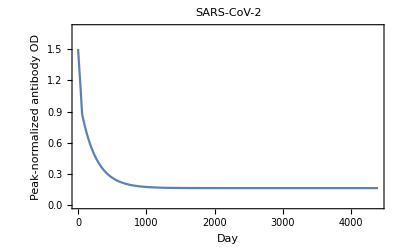

```mathematica
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster26Mar2024.pdf.

$Failed

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-5.841733+-5.323444*aod)])
```

These values for a and b come from the ancestral and descendent states natural infection analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(5.84173+5.32344 aod))

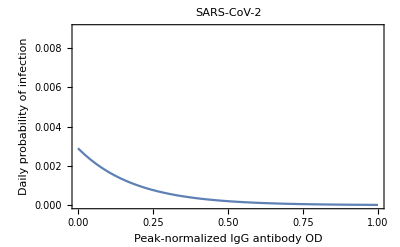

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster26Mar2024.pdf.

$Failed

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourseB],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,0.999999,0.999998,0.999997,0.999995,0.999994,0.999993,0.999991,0.99999,0.999988,0.999987,0.999985,0.999983,0.999981,0.999979,0.999976,0.999974,0.999972,0.999969,0.999966,0.999963,0.99996,0.999957,0.999953,0.99995,0.999946,0.999942,0.999937,0.999933,0.999928,0.999923,0.999918,0.999912,0.999906,0.9999,0.999893,0.999886,0.999879,0.999871,0.999863,0.999854,0.999845,0.999835,0.999824,0.999813,0.999801,0.999788,0.999775,0.999761,0.999745,0.999729,0.999712,0.999694,0.999674,0.999654,0.999632,0.999609,0.999585,0.999559,0.999532,0.999504,0.999476,0.999448,0.999418,0.999389,0.999359,0.999328,0.999297,0.999265,0.999233,0.999201,0.999167,0.999134,0.999099,0.999065,0.999029,0.998993,0.998957,0.99892,0.998882,0.998844,0.998805,0.998766,0.998726,0.998685,0.998644,0.998602,0.99856,0.998517,0.998473,0.998428,0.998383,0.998338,0.998291,0.998244,0.998196,0.998148,0.998099,0.998049,0.997998,0.997947,0.997895,0.997842,0.997789,0.997735,0.99768,0.997624,0.997568,0.99751,0.997452,0.997394,0.997334,0.997274,0.997212,0.99715,0.997087,0.997024,0.996959,0.996894,0.996828,0.996761,0.996693,0.996624,0.996554,0.996484,0.996412,0.99634,0.996267,0.996193,0.996117,0.996041,0.995965,0.995887,0.995808,0.995728,0.995647,0.995566,0.995483,0.995399,0.995314,0.995229,0.995142,0.995054,0.994966,0.994876,0.994785,0.994693,0.9946,0.994506,0.994411,0.994315,0.994218,0.99412,0.994021,0.99392,0.993819,0.993716,0.993612,0.993507,0.993401,0.993294,0.993186,0.993077,0.992966,0.992854,0.992741,0.992627,0.992512,0.992395,0.992277,0.992158,0.992038,0.991917,0.991794,0.99167,0.991545,0.991419,0.991291,0.991163,0.991032,0.990901,0.990768,0.990634,0.990499,0.990362,0.990225,0.990085,0.989945,0.989803,0.98966,0.989515,0.98937,0.989222,0.989074,0.988924,0.988773,0.98862,0.988466,0.98831,0.988153,0.987995,0.987836,0.987675,0.987512,0.987348,0.987183,0.987016,0.986848,0.986678,0.986507,0.986335,0.986161,0.985985,0.985808,0.98563,0.98545,0.985268,0.985086,0.984901,0.984715,0.984528,0.984339,0.984148,0.983957,0.983763,0.983568,0.983371,0.983173,0.982974,0.982773,0.98257,0.982365,0.98216,0.981952,0.981743,0.981532,0.98132,0.981107,0.980891,0.980674,0.980456,0.980236,0.980014,0.97979,0.979565,0.979339,0.979111,0.978881,0.978649,0.978416,0.978181,0.977945,0.977707,0.977467,0.977226,0.976983,0.976738,0.976492,0.976244,0.975994,0.975743,0.97549,0.975235,0.974979,0.974721,0.974461,0.9742,0.973937,0.973672,0.973406,0.973137,0.972868,0.972596,0.972323,0.972048,0.971771,0.971493,0.971213,0.970931,0.970647,0.970362,0.970075,0.969787,0.969496,0.969204,0.96891,0.968615,0.968317,0.968018,0.967718,0.967415,0.967111,0.966805,0.966497,0.966188,0.965877,0.965564,0.965249,0.964933,0.964615,0.964295,0.963973,0.96365,0.963325,0.962998,0.962669,0.962339,0.962007,0.961673,0.961338,0.961,0.960661,0.96032,0.959978,0.959634,0.959288,0.95894,0.95859,0.958239,0.957886,0.957531,0.957175,0.956817,0.956457,0.956095,0.955732,0.955366,0.954999,0.954631,0.95426,0.953888,0.953514,0.953139,0.952761,0.952382,0.952002,0.951619,0.951235,0.950849,0.950461,0.950072,0.94968,0.949288,0.948893,0.948497,0.948099,0.947699,0.947297,0.946894,0.946489,0.946083,0.945675,0.945265,0.944853,0.94444,0.944025,0.943608,0.943189,0.942769,0.942347,0.941924,0.941499,0.941072,0.940643,0.940213,0.939781,0.939348,0.938912,0.938476,0.938037,0.937597,0.937155,0.936712,0.936266,0.93582,0.935371,0.934921,0.934469,0.934016,0.933561,0.933105,0.932646,0.932187,0.931725,0.931262,0.930797,0.930331,0.929863,0.929394,0.928923,0.92845,0.927976,0.9275,0.927023,0.926544,0.926063,0.925581,0.925098,0.924612,0.924126,0.923637,0.923148,0.922656,0.922163,0.921669,0.921173,0.920675,0.920176,0.919676,0.919174,0.91867,0.918165,0.917658,0.91715,0.916641,0.91613,0.915617,0.915103,0.914588,0.914071,0.913552,0.913032,0.912511,0.911988,0.911464,0.910939,0.910412,0.909883,0.909353,0.908822,0.908289,0.907755,0.907219,0.906682,0.906144,0.905604,0.905063,0.904521,0.903977,0.903431,0.902885,0.902337,0.901788,0.901237,0.900685,0.900132,0.899577,0.899021,0.898463,0.897905,0.897345,0.896784,0.896221,0.895657,0.895092,0.894526,0.893958,0.893389,0.892819,0.892247,0.891674,0.8911,0.890525,0.889949,0.889371,0.888792,0.888212,0.88763,0.887048,0.886464,0.885879,0.885293,0.884705,0.884117,0.883527,0.882936,0.882344,0.881751,0.881156,0.880561,0.879964,0.879366,0.878767,0.878167,0.877566,0.876964,0.87636,0.875756,0.87515,0.874543,0.873936,0.873327,0.872717,0.872106,0.871494,0.87088,0.870266,0.869651,0.869035,0.868417,0.867799,0.86718,0.866559,0.865938,0.865316,0.864692,0.864068,0.863443,0.862816,0.862189,0.861561,0.860931,0.860301,0.85967,0.859038,0.858405,0.857771,0.857136,0.8565,0.855863,0.855226,0.854587,0.853948,0.853308,0.852666,0.852024,0.851381,0.850738,0.850093,0.849447,0.848801,0.848154,0.847506,0.846857,0.846207,0.845556,0.844905,0.844253,0.8436,0.842946,0.842292,0.841636,0.84098,0.840323,0.839665,0.839007,0.838348,0.837688,0.837027,0.836366,0.835704,0.835041,0.834377,0.833713,0.833048,0.832382,0.831716,0.831049,0.830381,0.829712,0.829043,0.828373,0.827703,0.827032,0.82636,0.825687,0.825014,0.82434,0.823666,0.822991,0.822315,0.821639,0.820962,0.820285,0.819607,0.818928,0.818249,0.817569,0.816889,0.816208,0.815527,0.814845,0.814162,0.813479,0.812795,0.812111,0.811426,0.810741,0.810055,0.809369,0.808682,0.807995,0.807307,0.806619,0.80593,0.805241,0.804551,0.803861,0.80317,0.802479,0.801787,0.801095,0.800403,0.79971,0.799016,0.798322,0.797628,0.796934,0.796239,0.795543,0.794847,0.794151,0.793454,0.792757,0.79206,0.791362,0.790664,0.789965,0.789267,0.788567,0.787868,0.787168,0.786467,0.785767,0.785066,0.784365,0.783663,0.782961,0.782259,0.781556,0.780853,0.78015,0.779447,0.778743,0.778039,0.777335,0.77663,0.775925,0.77522,0.774515,0.773809,0.773104,0.772398,0.771691,0.770985,0.770278,0.769571,0.768864,0.768156,0.767448,0.766741,0.766032,0.765324,0.764616,0.763907,0.763198,0.762489,0.76178,0.761071,0.760361,0.759651,0.758941,0.758231,0.757521,0.756811,0.7561,0.75539,0.754679,0.753968,0.753257,0.752546,0.751835,0.751124,0.750412,0.749701,0.748989,0.748277,0.747566,0.746854,0.746142,0.74543,0.744717,0.744005,0.743293,0.742581,0.741868,0.741156,0.740443,0.739731,0.739018,0.738306,0.737593,0.73688,0.736168,0.735455,0.734742,0.734029,0.733317,0.732604,0.731891,0.731178,0.730466,0.729753,0.72904,0.728327,0.727615,0.726902,0.726189,0.725477,0.724764,0.724051,0.723339,0.722626,0.721914,0.721202,0.720489,0.719777,0.719065,0.718353,0.717641,0.716929,0.716217,0.715505,0.714793,0.714081,0.71337,0.712658,0.711947,0.711236,0.710525,0.709813,0.709102,0.708392,0.707681,0.70697,0.70626,0.705549,0.704839,0.704129,0.703419,0.702709,0.702,0.70129,0.700581,0.699871,0.699162,0.698453,0.697745,0.697036,0.696328,0.695619,0.694911,0.694203,0.693496,0.692788,0.692081,0.691373,0.690666,0.68996,0.689253,0.688547,0.68784,0.687134,0.686429,0.685723,0.685018,0.684312,0.683607,0.682903,0.682198,0.681494,0.68079,0.680086,0.679382,0.678679,0.677976,0.677273,0.67657,0.675868,0.675166,0.674464,0.673762,0.673061,0.67236,0.671659,0.670959,0.670258,0.669558,0.668858,0.668159,0.66746,0.666761,0.666062,0.665364,0.664666,0.663968,0.66327,0.662573,0.661876,0.66118,0.660483,0.659787,0.659091,0.658396,0.657701,0.657006,0.656312,0.655618,0.654924,0.65423,0.653537,0.652844,0.652152,0.651459,0.650767,0.650076,0.649385,0.648694,0.648003,0.647313,0.646623,0.645934,0.645244,0.644556,0.643867,0.643179,0.642491,0.641804,0.641117,0.64043,0.639744,0.639058,0.638372,0.637687,0.637002,0.636317,0.635633,0.63495,0.634266,0.633583,0.632901,0.632218,0.631536,0.630855,0.630174,0.629493,0.628813,0.628133,0.627454,0.626774,0.626096,0.625417,0.624739,0.624062,0.623385,0.622708,0.622032,0.621356,0.62068,0.620005,0.619331,0.618656,0.617983,0.617309,0.616636,0.615964,0.615291,0.61462,0.613948,0.613278,0.612607,0.611937,0.611268,0.610598,0.60993,0.609261,0.608593,0.607926,0.607259,0.606593,0.605926,0.605261,0.604596,0.603931,0.603267,0.602603,0.601939,0.601276,0.600614,0.599952,0.59929,0.598629,0.597968,0.597308,0.596648,0.595989,0.59533,0.594672,0.594014,0.593356,0.592699,0.592043,0.591387,0.590731,0.590076,0.589421,0.588767,0.588113,0.58746,0.586807,0.586155,0.585503,0.584852,0.584201,0.583551,0.582901,0.582251,0.581603,0.580954,0.580306,0.579659,0.579012,0.578365,0.577719,0.577074,0.576429,0.575784,0.57514,0.574497,0.573854,0.573211,0.572569,0.571927,0.571286,0.570646,0.570006,0.569366,0.568727,0.568089,0.567451,0.566813,0.566176,0.56554,0.564904,0.564268,0.563633,0.562999,0.562365,0.561731,0.561098,0.560466,0.559834,0.559202,0.558571,0.557941,0.557311,0.556682,0.556053,0.555425,0.554797,0.554169,0.553543,0.552916,0.552291,0.551665,0.551041,0.550417,0.549793,0.54917,0.548547,0.547925,0.547303,0.546682,0.546062,0.545442,0.544823,0.544204,0.543585,0.542967,0.54235,0.541733,0.541117,0.540501,0.539886,0.539271,0.538657,0.538044,0.53743,0.536818,0.536206,0.535594,0.534983,0.534373,0.533763,0.533154,0.532545,0.531937,0.531329,0.530722,0.530115,0.529509,0.528903,0.528298,0.527694,0.52709,0.526487,0.525884,0.525281,0.52468,0.524078,0.523478,0.522878,0.522278,0.521679,0.52108,0.520482,0.519885,0.519288,0.518692,0.518096,0.517501,0.516906,0.516312,0.515718,0.515125,0.514532,0.51394,0.513349,0.512758,0.512168,0.511578,0.510989,0.5104,0.509812,0.509224,0.508637,0.508051,0.507465,0.506879,0.506295,0.50571,0.505127,0.504543,0.503961,0.503379,0.502797,0.502216,0.501636,0.501056,0.500476,0.499898,0.499319,0.498742,0.498165,0.497588,0.497012,0.496436,0.495862,0.495287,0.494713,0.49414,0.493567,0.492995,0.492424,0.491853,0.491282,0.490712,0.490143,0.489574,0.489006,0.488438,0.487871,0.487304,0.486738,0.486172,0.485608,0.485043,0.484479,0.483916,0.483353,0.482791,0.482229,0.481668,0.481108,0.480548,0.479988,0.479429,0.478871,0.478313,0.477756,0.4772,0.476643,0.476088,0.475533,0.474978,0.474425,0.473871,0.473319,0.472766,0.472215,0.471664,0.471113,0.470563,0.470013,0.469465,0.468916,0.468368,0.467821,0.467275,0.466728,0.466183,0.465638,0.465093,0.464549,0.464006,0.463463,0.462921,0.462379,0.461838,0.461297,0.460757,0.460218,0.459679,0.459141,0.458603,0.458065,0.457529,0.456993,0.456457,0.455922,0.455387,0.454853,0.45432,0.453787,0.453255,0.452723,0.452192,0.451661,0.451131,0.450601,0.450072,0.449544,0.449016,0.448488,0.447961,0.447435,0.446909,0.446384,0.44586,0.445336,0.444812,0.444289,0.443766,0.443245,0.442723,0.442202,0.441682,0.441162,0.440643,0.440125,0.439607,0.439089,0.438572,0.438056,0.43754,0.437024,0.436509,0.435995,0.435481,0.434968,0.434456,0.433944,0.433432,0.432921,0.43241,0.431901,0.431391,0.430882,0.430374,0.429866,0.429359,0.428852,0.428346,0.427841,0.427336,0.426831,0.426327,0.425824,0.425321,0.424818,0.424317,0.423815,0.423314,0.422814,0.422315,0.421815,0.421317,0.420819,0.420321,0.419824,0.419328,0.418832,0.418337,0.417842,0.417347,0.416854,0.41636,0.415868,0.415375,0.414884,0.414393,0.413902,0.413412,0.412923,0.412434,0.411945,0.411457,0.41097,0.410483,0.409997,0.409511,0.409026,0.408541,0.408057,0.407573,0.40709,0.406607,0.406125,0.405643,0.405162,0.404682,0.404202,0.403722,0.403243,0.402765,0.402287,0.40181,0.401333,0.400857,0.400381,0.399906,0.399431,0.398957,0.398483,0.39801,0.397537,0.397065,0.396593,0.396122,0.395652,0.395181,0.394712,0.394243,0.393774,0.393306,0.392839,0.392372,0.391906,0.39144,0.390974,0.390509,0.390045,0.389581,0.389118,0.388655,0.388193,0.387731,0.38727,0.386809,0.386349,0.385889,0.38543,0.384971,0.384513,0.384055,0.383598,0.383141,0.382685,0.382229,0.381774,0.38132,0.380865,0.380412,0.379959,0.379506,0.379054,0.378602,0.378151,0.377701,0.377251,0.376801,0.376352,0.375903,0.375455,0.375008,0.374561,0.374114,0.373668,0.373223,0.372778,0.372333,0.371889,0.371445,0.371002,0.37056,0.370118,0.369676,0.369235,0.368795,0.368355,0.367915,0.367476,0.367037,0.366599,0.366162,0.365725,0.365288,0.364852,0.364416,0.363981,0.363547,0.363113,0.362679,0.362246,0.361813,0.361381,0.360949,0.360518,0.360087,0.359657,0.359228,0.358798,0.35837,0.357941,0.357514,0.357086,0.35666,0.356233,0.355807,0.355382,0.354957,0.354533,0.354109,0.353686,0.353263,0.35284,0.352418,0.351997,0.351576,0.351155,0.350735,0.350316,0.349897,0.349478,0.34906,0.348643,0.348225,0.347809,0.347393,0.346977,0.346562,0.346147,0.345733,0.345319,0.344905,0.344493,0.34408,0.343668,0.343257,0.342846,0.342435,0.342025,0.341616,0.341207,0.340798,0.34039,0.339982,0.339575,0.339168,0.338762,0.338356,0.337951,0.337546,0.337142,0.336738,0.336334,0.335931,0.335529,0.335127,0.334725,0.334324,0.333923,0.333523,0.333123,0.332724,0.332325,0.331927,0.331529,0.331131,0.330734,0.330338,0.329942,0.329546,0.329151,0.328756,0.328362,0.327968,0.327575,0.327182,0.326789,0.326397,0.326006,0.325615,0.325224,0.324834,0.324444,0.324055,0.323666,0.323278,0.32289,0.322503,0.322116,0.321729,0.321343,0.320957,0.320572,0.320187,0.319803,0.319419,0.319036,0.318653,0.31827,0.317888,0.317506,0.317125,0.316745,0.316364,0.315984,0.315605,0.315226,0.314847,0.314469,0.314092,0.313714,0.313338,0.312961,0.312585,0.31221,0.311835,0.31146,0.311086,0.310713,0.310339,0.309966,0.309594,0.309222,0.308851,0.308479,0.308109,0.307739,0.307369,0.306999,0.30663,0.306262,0.305894,0.305526,0.305159,0.304792,0.304426,0.30406,0.303694,0.303329,0.302965,0.3026,0.302237,0.301873,0.30151,0.301148,0.300786,0.300424,0.300063,0.299702,0.299342,0.298982,0.298622,0.298263,0.297904,0.297546,0.297188,0.296831,0.296474,0.296117,0.295761,0.295405,0.29505,0.294695,0.29434,0.293986,0.293633,0.293279,0.292927,0.292574,0.292222,0.29187,0.291519,0.291168,0.290818,0.290468,0.290119,0.289769,0.289421,0.289072,0.288725,0.288377,0.28803,0.287683,0.287337,0.286991,0.286646,0.286301,0.285956,0.285612,0.285268,0.284925,0.284582,0.284239,0.283897,0.283555,0.283214,0.282873,0.282532,0.282192,0.281852,0.281513,0.281174,0.280835,0.280497,0.280159,0.279822,0.279485,0.279148,0.278812,0.278476,0.278141,0.277806,0.277471,0.277137,0.276803,0.27647,0.276137,0.275804,0.275472,0.27514,0.274809,0.274477,0.274147,0.273817,0.273487,0.273157,0.272828,0.272499,0.272171,0.271843,0.271516,0.271188,0.270862,0.270535,0.270209,0.269884,0.269558,0.269233,0.268909,0.268585,0.268261,0.267938,0.267615,0.267292,0.26697,0.266649,0.266327,0.266006,0.265686,0.265365,0.265045,0.264726,0.264407,0.264088,0.26377,0.263452,0.263134,0.262817,0.2625,0.262184,0.261867,0.261552,0.261236,0.260921,0.260607,0.260293,0.259979,0.259665,0.259352,0.259039,0.258727,0.258415,0.258104,0.257792,0.257481,0.257171,0.256861,0.256551,0.256242,0.255933,0.255624,0.255316,0.255008,0.2547,0.254393,0.254086,0.25378,0.253473,0.253168,0.252862,0.252557,0.252253,0.251948,0.251644,0.251341,0.251038,0.250735,0.250432,0.25013,0.249829,0.249527,0.249226,0.248925,0.248625,0.248325,0.248026,0.247726,0.247427,0.247129,0.246831,0.246533,0.246235,0.245938,0.245641,0.245345,0.245049,0.244753,0.244458,0.244163,0.243868,0.243574,0.24328,0.242986,0.242693,0.2424,0.242108,0.241816,0.241524,0.241232,0.240941,0.24065,0.24036,0.24007,0.23978,0.239491,0.239202,0.238913,0.238624,0.238336,0.238049,0.237761,0.237474,0.237188,0.236901,0.236615,0.23633,0.236044,0.235759,0.235475,0.235191,0.234907,0.234623,0.23434,0.234057,0.233774,0.233492,0.23321,0.232929,0.232647,0.232367,0.232086,0.231806,0.231526,0.231246,0.230967,0.230688,0.23041,0.230131,0.229854,0.229576,0.229299,0.229022,0.228745,0.228469,0.228193,0.227918,0.227642,0.227368,0.227093,0.226819,0.226545,0.226271,0.225998,0.225725,0.225452,0.22518,0.224908,0.224637,0.224365,0.224094,0.223824,0.223553,0.223283,0.223014,0.222744,0.222475,0.222206,0.221938,0.22167,0.221402,0.221135,0.220868,0.220601,0.220334,0.220068,0.219802,0.219537,0.219272,0.219007,0.218742,0.218478,0.218214,0.21795,0.217687,0.217424,0.217162,0.216899,0.216637,0.216375,0.216114,0.215853,0.215592,0.215332,0.215072,0.214812,0.214552,0.214293,0.214034,0.213775,0.213517,0.213259,0.213002,0.212744,0.212487,0.21223,0.211974,0.211718,0.211462,0.211206,0.210951,0.210696,0.210442,0.210188,0.209934,0.20968,0.209426,0.209173,0.208921,0.208668,0.208416,0.208164,0.207913,0.207661,0.20741,0.20716,0.206909,0.206659,0.20641,0.20616,0.205911,0.205662,0.205414,0.205165,0.204917,0.20467,0.204422,0.204175,0.203929,0.203682,0.203436,0.20319,0.202945,0.202699,0.202454,0.20221,0.201965,0.201721,0.201477,0.201234,0.200991,0.200748,0.200505,0.200263,0.200021,0.199779,0.199537,0.199296,0.199055,0.198815,0.198574,0.198334,0.198094,0.197855,0.197616,0.197377,0.197138,0.1969,0.196662,0.196424,0.196187,0.19595,0.195713,0.195476,0.19524,0.195004,0.194768,0.194533,0.194298,0.194063,0.193828,0.193594,0.19336,0.193126,0.192893,0.192659,0.192426,0.192194,0.191961,0.191729,0.191498,0.191266,0.191035,0.190804,0.190573,0.190343,0.190113,0.189883,0.189653,0.189424,0.189195,0.188966,0.188738,0.188509,0.188282,0.188054,0.187826,0.187599,0.187373,0.187146,0.18692,0.186694,0.186468,0.186243,0.186017,0.185792,0.185568,0.185343,0.185119,0.184895,0.184672,0.184449,0.184226,0.184003,0.18378,0.183558,0.183336,0.183114,0.182893,0.182672,0.182451,0.18223,0.18201,0.18179,0.18157,0.18135,0.181131,0.180912,0.180693,0.180475,0.180257,0.180039,0.179821,0.179603,0.179386,0.179169,0.178953,0.178736,0.17852,0.178304,0.178089,0.177873,0.177658,0.177443,0.177229,0.177014,0.1768,0.176586,0.176373,0.176159,0.175946,0.175734,0.175521,0.175309,0.175097,0.174885,0.174674,0.174462,0.174251,0.174041,0.17383,0.17362,0.17341,0.1732,0.172991,0.172781,0.172572,0.172364,0.172155,0.171947,0.171739,0.171531,0.171324,0.171117,0.17091,0.170703,0.170496,0.17029,0.170084,0.169879,0.169673,0.169468,0.169263,0.169058,0.168854,0.168649,0.168445,0.168242,0.168038,0.167835,0.167632,0.167429,0.167227,0.167024,0.166822,0.166621,0.166419,0.166218,0.166017,0.165816,0.165615,0.165415,0.165215,0.165015,0.164815,0.164616,0.164417,0.164218,0.164019,0.163821,0.163623,0.163425,0.163227,0.16303,0.162832,0.162636,0.162439,0.162242,0.162046,0.16185,0.161654,0.161459,0.161263,0.161068,0.160873,0.160679,0.160484,0.16029,0.160096,0.159903,0.159709,0.159516,0.159323,0.15913,0.158938,0.158746,0.158553,0.158362,0.15817,0.157979,0.157788,0.157597,0.157406,0.157216,0.157025,0.156836,0.156646,0.156456,0.156267,0.156078,0.155889,0.155701,0.155512,0.155324,0.155136,0.154948,0.154761,0.154574,0.154387,0.1542,0.154013,0.153827,0.153641,0.153455,0.153269,0.153084,0.152899,0.152714,0.152529,0.152344,0.15216,0.151976,0.151792,0.151609,0.151425,0.151242,0.151059,0.150876,0.150694,0.150511,0.150329,0.150147,0.149966,0.149784,0.149603,0.149422,0.149241,0.149061,0.14888,0.1487,0.14852,0.148341,0.148161,0.147982,0.147803,0.147624,0.147445,0.147267,0.147089,0.146911,0.146733,0.146555,0.146378,0.146201,0.146024,0.145847,0.145671,0.145495,0.145319,0.145143,0.144967,0.144792,0.144617,0.144442,0.144267,0.144092,0.143918,0.143744,0.14357,0.143396,0.143223,0.143049,0.142876,0.142703,0.142531,0.142358,0.142186,0.142014,0.141842,0.14167,0.141499,0.141328,0.141157,0.140986,0.140815,0.140645,0.140475,0.140305,0.140135,0.139966,0.139796,0.139627,0.139458,0.139289,0.139121,0.138952,0.138784,0.138616,0.138449,0.138281,0.138114,0.137947,0.13778,0.137613,0.137446,0.13728,0.137114,0.136948,0.136782,0.136617,0.136452,0.136286,0.136121,0.135957,0.135792,0.135628,0.135464,0.1353,0.135136,0.134973,0.134809,0.134646,0.134483,0.13432,0.134158,0.133996,0.133833,0.133671,0.13351,0.133348,0.133187,0.133026,0.132865,0.132704,0.132543,0.132383,0.132223,0.132063,0.131903,0.131743,0.131584,0.131425,0.131266,0.131107,0.130948,0.13079,0.130631,0.130473,0.130315,0.130158,0.13,0.129843,0.129686,0.129529,0.129372,0.129215,0.129059,0.128903,0.128747,0.128591,0.128435,0.12828,0.128125,0.12797,0.127815,0.12766,0.127506,0.127351,0.127197,0.127043,0.12689,0.126736,0.126583,0.126429,0.126276,0.126124,0.125971,0.125819,0.125666,0.125514,0.125362,0.125211,0.125059,0.124908,0.124757,0.124606,0.124455,0.124304,0.124154,0.124003,0.123853,0.123703,0.123554,0.123404,0.123255,0.123106,0.122957,0.122808,0.122659,0.122511,0.122363,0.122215,0.122067,0.121919,0.121771,0.121624,0.121477,0.12133,0.121183,0.121036,0.12089,0.120743,0.120597,0.120451,0.120306,0.12016,0.120015,0.119869,0.119724,0.119579,0.119435,0.11929,0.119146,0.119002,0.118857,0.118714,0.11857,0.118426,0.118283,0.11814,0.117997,0.117854,0.117712,0.117569,0.117427,0.117285,0.117143,0.117001,0.116859,0.116718,0.116577,0.116436,0.116295,0.116154,0.116013,0.115873,0.115733,0.115593,0.115453,0.115313,0.115173,0.115034,0.114895,0.114756,0.114617,0.114478,0.11434,0.114201,0.114063,0.113925,0.113787,0.113649,0.113512,0.113374,0.113237,0.1131,0.112963,0.112827,0.11269,0.112554,0.112417,0.112281,0.112145,0.11201,0.111874,0.111739,0.111603,0.111468,0.111333,0.111199,0.111064,0.11093,0.110795,0.110661,0.110527,0.110394,0.11026,0.110127,0.109993,0.10986,0.109727,0.109594,0.109462,0.109329,0.109197,0.109065,0.108933,0.108801,0.108669,0.108538,0.108406,0.108275,0.108144,0.108013,0.107882,0.107752,0.107621,0.107491,0.107361,0.107231,0.107101,0.106972,0.106842,0.106713,0.106584,0.106455,0.106326,0.106197,0.106069,0.10594,0.105812,0.105684,0.105556,0.105428,0.105301,0.105173,0.105046,0.104919,0.104792,0.104665,0.104538,0.104412,0.104285,0.104159,0.104033,0.103907,0.103781,0.103656,0.10353,0.103405,0.10328,0.103155,0.10303,0.102905,0.102781,0.102656,0.102532,0.102408,0.102284,0.10216,0.102037,0.101913,0.10179,0.101667,0.101544,0.101421,0.101298,0.101175,0.101053,0.100931,0.100808,0.100686,0.100564,0.100443,0.100321,0.1002,0.100078,0.0999573,0.0998363,0.0997155,0.0995948,0.0994743,0.0993539,0.0992336,0.0991135,0.0989935,0.0988737,0.098754,0.0986345,0.0985151,0.0983959,0.0982768,0.0981578,0.098039,0.0979203,0.0978018,0.0976834,0.0975652,0.0974471,0.0973292,0.0972113,0.0970937,0.0969762,0.0968588,0.0967415,0.0966244,0.0965075,0.0963907,0.096274,0.0961575,0.0960411,0.0959248,0.0958087,0.0956928,0.0955769,0.0954612,0.0953457,0.0952303,0.095115,0.0949999,0.0948849,0.0947701,0.0946553,0.0945408,0.0944263,0.094312,0.0941979,0.0940839,0.09397,0.0938563,0.0937426,0.0936292,0.0935158,0.0934027,0.0932896,0.0931767,0.0930639,0.0929512,0.0928387,0.0927264,0.0926141,0.092502,0.0923901,0.0922782,0.0921665,0.092055,0.0919435,0.0918323,0.0917211,0.0916101,0.0914992,0.0913884,0.0912778,0.0911673,0.091057,0.0909468,0.0908367,0.0907267,0.0906169,0.0905072,0.0903977,0.0902883,0.090179,0.0900698,0.0899608,0.0898519,0.0897431,0.0896345,0.089526,0.0894176,0.0893094,0.0892013,0.0890933,0.0889855,0.0888778,0.0887702,0.0886628,0.0885554,0.0884482,0.0883412,0.0882342,0.0881274,0.0880208,0.0879142,0.0878078,0.0877015,0.0875954,0.0874893,0.0873834,0.0872777,0.087172,0.0870665,0.0869611,0.0868559,0.0867507,0.0866457,0.0865408,0.0864361,0.0863315,0.086227,0.0861226,0.0860183,0.0859142,0.0858102,0.0857064,0.0856026,0.085499,0.0853955,0.0852921,0.0851889,0.0850858,0.0849828,0.0848799,0.0847772,0.0846746,0.0845721,0.0844697,0.0843674,0.0842653,0.0841633,0.0840614,0.0839597,0.0838581,0.0837566,0.0836552,0.0835539,0.0834528,0.0833518,0.0832509,0.0831501,0.0830494,0.0829489,0.0828485,0.0827482,0.0826481,0.082548,0.0824481,0.0823483,0.0822486,0.0821491,0.0820496,0.0819503,0.0818511,0.081752,0.0816531,0.0815542,0.0814555,0.0813569,0.0812584,0.0811601,0.0810618,0.0809637,0.0808657,0.0807678,0.0806701,0.0805724,0.0804749,0.0803775,0.0802802,0.080183,0.0800859,0.079989,0.0798922,0.0797955,0.0796989,0.0796024,0.0795061,0.0794098,0.0793137,0.0792177,0.0791218,0.079026,0.0789304,0.0788348,0.0787394,0.0786441,0.0785489,0.0784538,0.0783588,0.078264,0.0781693,0.0780746,0.0779801,0.0778857,0.0777915,0.0776973,0.0776032,0.0775093,0.0774155,0.0773218,0.0772282,0.0771347,0.0770413,0.0769481,0.0768549,0.0767619,0.076669,0.0765762,0.0764835,0.0763909,0.0762984,0.0762061,0.0761138,0.0760217,0.0759297,0.0758378,0.075746,0.0756543,0.0755627,0.0754712,0.0753799,0.0752886,0.0751975,0.0751065,0.0750155,0.0749247,0.074834,0.0747435,0.074653,0.0745626,0.0744724,0.0743822,0.0742922,0.0742022,0.0741124,0.0740227,0.0739331,0.0738436,0.0737542,0.073665,0.0735758,0.0734867,0.0733978,0.0733089,0.0732202,0.0731316,0.073043,0.0729546,0.0728663,0.0727781,0.07269,0.072602,0.0725141,0.0724263,0.0723387,0.0722511,0.0721637,0.0720763,0.0719891,0.0719019,0.0718149,0.0717279,0.0716411,0.0715544,0.0714678,0.0713813,0.0712949,0.0712086,0.0711224,0.0710363,0.0709503,0.0708644,0.0707786,0.0706929,0.0706074,0.0705219,0.0704365,0.0703513,0.0702661,0.0701811,0.0700961,0.0700113,0.0699265,0.0698419,0.0697573,0.0696729,0.0695885,0.0695043,0.0694202,0.0693361,0.0692522,0.0691684,0.0690846,0.069001,0.0689175,0.0688341,0.0687508,0.0686675,0.0685844,0.0685014,0.0684185,0.0683356,0.0682529,0.0681703,0.0680878,0.0680054,0.067923,0.0678408,0.0677587,0.0676767,0.0675948,0.0675129,0.0674312,0.0673496,0.0672681,0.0671866,0.0671053,0.0670241,0.0669429,0.0668619,0.066781,0.0667001,0.0666194,0.0665388,0.0664582,0.0663778,0.0662974,0.0662172,0.066137,0.0660569,0.065977,0.0658971,0.0658174,0.0657377,0.0656581,0.0655786,0.0654992,0.06542,0.0653408,0.0652617,0.0651827,0.0651038,0.065025,0.0649462,0.0648676,0.0647891,0.0647107,0.0646323,0.0645541,0.064476,0.0643979,0.06432,0.0642421,0.0641643,0.0640867,0.0640091,0.0639316,0.0638542,0.0637769,0.0636997,0.0636226,0.0635456,0.0634687,0.0633919,0.0633151,0.0632385,0.0631619,0.0630855,0.0630091,0.0629328,0.0628566,0.0627806,0.0627046,0.0626287,0.0625528,0.0624771,0.0624015,0.062326,0.0622505,0.0621752,0.0620999,0.0620247,0.0619496,0.0618747,0.0617998,0.0617249,0.0616502,0.0615756,0.0615011,0.0614266,0.0613523,0.061278,0.0612038,0.0611297,0.0610557,0.0609818,0.060908,0.0608343,0.0607606,0.0606871,0.0606136,0.0605402,0.060467,0.0603938,0.0603207,0.0602476,0.0601747,0.0601019,0.0600291,0.0599564,0.0598839,0.0598114,0.059739,0.0596667,0.0595944,0.0595223,0.0594502,0.0593783,0.0593064,0.0592346,0.0591629,0.0590913,0.0590198,0.0589483,0.058877,0.0588057,0.0587345,0.0586634,0.0585924,0.0585215,0.0584506,0.0583799,0.0583092,0.0582386,0.0581681,0.0580977,0.0580274,0.0579571,0.057887,0.0578169,0.0577469,0.057677,0.0576072,0.0575375,0.0574678,0.0573982,0.0573288,0.0572594,0.0571901,0.0571208,0.0570517,0.0569826,0.0569136,0.0568448,0.0567759,0.0567072,0.0566386,0.05657,0.0565015,0.0564331,0.0563648,0.0562966,0.0562284,0.0561604,0.0560924,0.0560245,0.0559567,0.0558889,0.0558213,0.0557537,0.0556862,0.0556188,0.0555515,0.0554842,0.0554171,0.05535,0.055283,0.0552161,0.0551492,0.0550825,0.0550158,0.0549492,0.0548827,0.0548162,0.0547499,0.0546836,0.0546174,0.0545513,0.0544853,0.0544193,0.0543534,0.0542876,0.0542219,0.0541563,0.0540907,0.0540253,0.0539599,0.0538945,0.0538293,0.0537641,0.0536991,0.0536341,0.0535691,0.0535043,0.0534395,0.0533748,0.0533102,0.0532457,0.0531812,0.0531168,0.0530526,0.0529883,0.0529242,0.0528601,0.0527961,0.0527322,0.0526684,0.0526046,0.052541,0.0524774,0.0524138,0.0523504,0.052287,0.0522237,0.0521605,0.0520974,0.0520343,0.0519713,0.0519084,0.0518456,0.0517828,0.0517201,0.0516575,0.051595,0.0515325,0.0514701,0.0514078,0.0513456,0.0512834,0.0512214,0.0511594,0.0510974,0.0510356,0.0509738,0.0509121,0.0508505,0.0507889,0.0507274,0.050666,0.0506047,0.0505434,0.0504823,0.0504211,0.0503601,0.0502991,0.0502383,0.0501774,0.0501167,0.050056,0.0499954,0.0499349,0.0498745,0.0498141,0.0497538,0.0496936,0.0496334,0.0495733,0.0495133,0.0494534,0.0493935,0.0493337,0.049274,0.0492144,0.0491548,0.0490953,0.0490359,0.0489765,0.0489172,0.048858,0.0487989,0.0487398,0.0486808,0.0486219,0.048563,0.0485042,0.0484455,0.0483868,0.0483283,0.0482698,0.0482113,0.048153,0.0480947,0.0480365,0.0479783,0.0479202,0.0478622,0.0478043,0.0477464,0.0476886,0.0476309,0.0475732,0.0475157,0.0474581,0.0474007,0.0473433,0.047286,0.0472288,0.0471716,0.0471145,0.0470575,0.0470005,0.0469436,0.0468868,0.04683,0.0467733,0.0467167,0.0466602,0.0466037,0.0465473,0.0464909,0.0464346,0.0463784,0.0463223,0.0462662,0.0462102,0.0461543,0.0460984,0.0460426,0.0459869,0.0459312,0.0458756,0.0458201,0.0457646,0.0457092,0.0456539,0.0455986,0.0455434,0.0454883,0.0454332,0.0453782,0.0453233,0.0452684,0.0452136,0.0451589,0.0451042,0.0450496,0.0449951,0.0449406,0.0448862,0.0448319,0.0447776,0.0447234,0.0446693,0.0446152,0.0445612,0.0445072,0.0444534,0.0443995,0.0443458,0.0442921,0.0442385,0.0441849,0.0441315,0.044078,0.0440247,0.0439714,0.0439182,0.043865,0.0438119,0.0437589,0.0437059,0.043653,0.0436001,0.0435474,0.0434946,0.043442,0.0433894,0.0433369,0.0432844,0.043232,0.0431797,0.0431274,0.0430752,0.0430231,0.042971,0.042919,0.042867,0.0428151,0.0427633,0.0427115,0.0426598,0.0426082,0.0425566,0.0425051,0.0424536,0.0424023,0.0423509,0.0422997,0.0422485,0.0421973,0.0421462,0.0420952,0.0420443,0.0419934,0.0419425,0.0418918,0.041841,0.0417904,0.0417398,0.0416893,0.0416388,0.0415884,0.0415381,0.0414878,0.0414376,0.0413874,0.0413373,0.0412873,0.0412373,0.0411874,0.0411375,0.0410877,0.041038,0.0409883,0.0409387,0.0408891,0.0408396,0.0407902,0.0407408,0.0406915,0.0406422,0.040593,0.0405439,0.0404948,0.0404458,0.0403968,0.0403479,0.0402991,0.0402503,0.0402016,0.0401529,0.0401043,0.0400558,0.0400073,0.0399588,0.0399105,0.0398622,0.0398139,0.0397657,0.0397176,0.0396695,0.0396215,0.0395735,0.0395256,0.0394778,0.03943,0.0393822,0.0393346,0.039287,0.0392394,0.0391919,0.0391445,0.0390971,0.0390497,0.0390025,0.0389553,0.0389081,0.038861,0.038814,0.038767,0.03872,0.0386732,0.0386264,0.0385796,0.0385329,0.0384863,0.0384397,0.0383931,0.0383467,0.0383002,0.0382539,0.0382076,0.0381613,0.0381151,0.038069,0.0380229,0.0379769,0.0379309,0.037885,0.0378391,0.0377933,0.0377476,0.0377019,0.0376562,0.0376107,0.0375651,0.0375197,0.0374742,0.0374289,0.0373836,0.0373383,0.0372931,0.037248,0.0372029,0.0371578,0.0371129,0.0370679,0.0370231,0.0369782,0.0369335,0.0368888,0.0368441,0.0367995,0.036755,0.0367105,0.036666,0.0366217,0.0365773,0.036533,0.0364888,0.0364446,0.0364005,0.0363565,0.0363125,0.0362685,0.0362246,0.0361807,0.0361369,0.0360932,0.0360495,0.0360059,0.0359623,0.0359188,0.0358753,0.0358318,0.0357885,0.0357451,0.0357019,0.0356587,0.0356155,0.0355724,0.0355293,0.0354863,0.0354434,0.0354004,0.0353576,0.0353148,0.035272,0.0352293,0.0351867,0.0351441,0.0351016,0.0350591,0.0350166,0.0349742,0.0349319,0.0348896,0.0348474,0.0348052,0.0347631,0.034721,0.034679,0.034637,0.0345951,0.0345532,0.0345113,0.0344696,0.0344278,0.0343862,0.0343445,0.034303,0.0342614,0.03422,0.0341785,0.0341372,0.0340958,0.0340546,0.0340133,0.0339722,0.033931,0.03389,0.033849,0.033808,0.033767,0.0337262,0.0336853,0.0336446,0.0336038,0.0335632,0.0335225,0.033482,0.0334414,0.0334009,0.0333605,0.0333201,0.0332798,0.0332395,0.0331993,0.0331591,0.0331189,0.0330788,0.0330388,0.0329988,0.0329589,0.032919,0.0328791,0.0328393,0.0327996,0.0327599,0.0327202,0.0326806,0.032641,0.0326015,0.0325621,0.0325226,0.0324833,0.0324439,0.0324047,0.0323654,0.0323263,0.0322871,0.0322481,0.032209,0.03217,0.0321311,0.0320922,0.0320533,0.0320145,0.0319758,0.0319371,0.0318984,0.0318598,0.0318212,0.0317827,0.0317442,0.0317058,0.0316674,0.0316291,0.0315908,0.0315526,0.0315144,0.0314762,0.0314381,0.0314001,0.0313621,0.0313241,0.0312862,0.0312483,0.0312105,0.0311727,0.031135,0.0310973,0.0310596,0.031022,0.0309845,0.030947,0.0309095,0.0308721,0.0308347,0.0307974,0.0307601,0.0307229,0.0306857,0.0306485,0.0306114,0.0305744,0.0305374,0.0305004,0.0304635,0.0304266,0.0303898,0.030353,0.0303162,0.0302795,0.0302429,0.0302063,0.0301697,0.0301332,0.0300967,0.0300603,0.0300239,0.0299875,0.0299512,0.029915,0.0298788,0.0298426,0.0298065,0.0297704,0.0297344,0.0296984,0.0296624,0.0296265,0.0295906,0.0295548,0.0295191,0.0294833,0.0294476,0.029412,0.0293764,0.0293408,0.0293053,0.0292698,0.0292344,0.029199,0.0291637,0.0291284,0.0290931,0.0290579,0.0290227,0.0289876,0.0289525,0.0289174,0.0288824,0.0288475,0.0288125,0.0287777,0.0287428,0.028708,0.0286733,0.0286386,0.0286039,0.0285693,0.0285347,0.0285002,0.0284656,0.0284312,0.0283968,0.0283624,0.0283281,0.0282938,0.0282595,0.0282253,0.0281911,0.028157,0.0281229,0.0280889,0.0280549,0.0280209,0.027987,0.0279531,0.0279193,0.0278855,0.0278517,0.027818,0.0277844,0.0277507,0.0277171,0.0276836,0.0276501,0.0276166,0.0275832,0.0275498,0.0275164,0.0274831,0.0274498,0.0274166,0.0273834,0.0273503,0.0273172,0.0272841,0.0272511,0.0272181,0.0271851,0.0271522,0.0271194,0.0270865,0.0270537,0.027021,0.0269883,0.0269556,0.026923,0.0268904,0.0268578,0.0268253,0.0267929,0.0267604,0.026728,0.0266957,0.0266634,0.0266311,0.0265988,0.0265666,0.0265345,0.0265024,0.0264703,0.0264382,0.0264062,0.0263743,0.0263423,0.0263105,0.0262786,0.0262468,0.026215,0.0261833,0.0261516,0.0261199,0.0260883,0.0260567,0.0260252,0.0259937,0.0259622,0.0259308,0.0258994,0.0258681,0.0258367,0.0258055,0.0257742,0.025743,0.0257119,0.0256807,0.0256496,0.0256186,0.0255876,0.0255566,0.0255257,0.0254948,0.0254639,0.0254331,0.0254023,0.0253716,0.0253408,0.0253102,0.0252795,0.0252489,0.0252184,0.0251878,0.0251573,0.0251269,0.0250965,0.0250661,0.0250357,0.0250054,0.0249752,0.0249449,0.0249147,0.0248846,0.0248545,0.0248244,0.0247943,0.0247643,0.0247343,0.0247044,0.0246745,0.0246446,0.0246148,0.024585,0.0245552,0.0245255,0.0244958,0.0244662,0.0244365,0.024407,0.0243774,0.0243479,0.0243184,0.024289,0.0242596,0.0242302,0.0242009,0.0241716,0.0241423,0.0241131,0.0240839,0.0240548,0.0240256,0.0239966,0.0239675,0.0239385,0.0239095,0.0238806,0.0238517,0.0238228,0.023794,0.0237652,0.0237364,0.0237077,0.023679,0.0236503,0.0236217,0.0235931,0.0235645,0.023536,0.0235075,0.023479,0.0234506,0.0234222,0.0233939,0.0233656,0.0233373,0.023309,0.0232808,0.0232526,0.0232245,0.0231964,0.0231683,0.0231402,0.0231122,0.0230842,0.0230563,0.0230284,0.0230005,0.0229727,0.0229449,0.0229171,0.0228893,0.0228616,0.022834,0.0228063,0.0227787,0.0227511,0.0227236,0.0226961,0.0226686,0.0226412,0.0226138,0.0225864,0.0225591,0.0225317,0.0225045,0.0224772,0.02245,0.0224228,0.0223957,0.0223686,0.0223415,0.0223145,0.0222875,0.0222605,0.0222335,0.0222066,0.0221797,0.0221529,0.0221261,0.0220993,0.0220725,0.0220458,0.0220191,0.0219925,0.0219658,0.0219393,0.0219127,0.0218862,0.0218597,0.0218332,0.0218068,0.0217804,0.021754,0.0217277,0.0217014,0.0216751,0.0216489,0.0216227,0.0215965,0.0215704,0.0215442,0.0215182,0.0214921,0.0214661,0.0214401,0.0214142,0.0213882,0.0213623,0.0213365,0.0213107,0.0212849,0.0212591,0.0212334,0.0212077,0.021182,0.0211563,0.0211307,0.0211052,0.0210796,0.0210541,0.0210286,0.0210031,0.0209777,0.0209523,0.020927,0.0209016,0.0208763,0.0208511,0.0208258,0.0208006,0.0207754,0.0207503,0.0207252,0.0207001,0.020675,0.02065,0.020625,0.0206,0.0205751,0.0205502,0.0205253,0.0205005,0.0204756,0.0204508,0.0204261,0.0204014,0.0203767,0.020352,0.0203274,0.0203028,0.0202782,0.0202536,0.0202291,0.0202046,0.0201802,0.0201557,0.0201313,0.020107,0.0200826,0.0200583,0.020034,0.0200098,0.0199856,0.0199614,0.0199372,0.0199131,0.019889,0.0198649,0.0198408,0.0198168,0.0197928,0.0197689,0.019745,0.019721,0.0196972,0.0196733,0.0196495,0.0196257,0.019602,0.0195782,0.0195545,0.0195309,0.0195072,0.0194836,0.01946,0.0194365,0.0194129,0.0193894,0.019366,0.0193425,0.0193191,0.0192957,0.0192724,0.019249,0.0192257,0.0192025,0.0191792,0.019156,0.0191328,0.0191097,0.0190865,0.0190634,0.0190403,0.0190173,0.0189943,0.0189713,0.0189483,0.0189254,0.0189025,0.0188796,0.0188567,0.0188339,0.0188111,0.0187883,0.0187656,0.0187429,0.0187202,0.0186975,0.0186749,0.0186523,0.0186297,0.0186072,0.0185846,0.0185621,0.0185397,0.0185172,0.0184948,0.0184724,0.0184501,0.0184277,0.0184054,0.0183831,0.0183609,0.0183387,0.0183165,0.0182943,0.0182721,0.01825,0.0182279,0.0182059,0.0181838,0.0181618,0.0181398,0.0181179,0.0180959,0.018074,0.0180521,0.0180303,0.0180085,0.0179867,0.0179649,0.0179431,0.0179214,0.0178997,0.0178781,0.0178564,0.0178348,0.0178132,0.0177917,0.0177701,0.0177486,0.0177271,0.0177057,0.0176842,0.0176628,0.0176414,0.0176201,0.0175988,0.0175775,0.0175562,0.0175349,0.0175137,0.0174925,0.0174713,0.0174502,0.017429,0.0174079,0.0173869,0.0173658,0.0173448,0.0173238,0.0173028,0.0172819,0.017261,0.0172401,0.0172192,0.0171984,0.0171775,0.0171568,0.017136,0.0171152,0.0170945,0.0170738,0.0170532,0.0170325,0.0170119,0.0169913,0.0169707,0.0169502,0.0169297,0.0169092,0.0168887,0.0168683,0.0168478,0.0168275,0.0168071,0.0167867,0.0167664,0.0167461,0.0167258,0.0167056,0.0166854,0.0166652,0.016645,0.0166249,0.0166047,0.0165846,0.0165646,0.0165445,0.0165245,0.0165045,0.0164845,0.0164645,0.0164446,0.0164247,0.0164048,0.016385,0.0163651,0.0163453,0.0163255,0.0163058,0.016286,0.0162663,0.0162466,0.016227,0.0162073,0.0161877,0.0161681,0.0161485,0.016129,0.0161095,0.01609,0.0160705,0.016051,0.0160316,0.0160122,0.0159928,0.0159734,0.0159541,0.0159348,0.0159155,0.0158962,0.015877,0.0158578,0.0158386,0.0158194,0.0158003,0.0157811,0.015762,0.0157429,0.0157239,0.0157049,0.0156858,0.0156669,0.0156479,0.0156289,0.01561,0.0155911,0.0155723,0.0155534,0.0155346,0.0155158,0.015497,0.0154782,0.0154595,0.0154408,0.0154221,0.0154034,0.0153848,0.0153662,0.0153475,0.015329,0.0153104,0.0152919,0.0152734,0.0152549,0.0152364,0.015218,0.0151995,0.0151811,0.0151628,0.0151444,0.0151261,0.0151078,0.0150895,0.0150712,0.015053,0.0150348,0.0150166,0.0149984,0.0149802,0.0149621,0.014944,0.0149259,0.0149078,0.0148898,0.0148717,0.0148537,0.0148358,0.0148178,0.0147999,0.0147819,0.0147641,0.0147462,0.0147283,0.0147105,0.0146927,0.0146749,0.0146571,0.0146394,0.0146217,0.014604,0.0145863,0.0145686,0.014551,0.0145334,0.0145158,0.0144982,0.0144807,0.0144632,0.0144456,0.0144282,0.0144107,0.0143932,0.0143758,0.0143584,0.014341,0.0143237,0.0143063,0.014289,0.0142717,0.0142544,0.0142372,0.01422,0.0142027,0.0141856,0.0141684,0.0141512,0.0141341,0.014117,0.0140999,0.0140828,0.0140658,0.0140488,0.0140317,0.0140148,0.0139978,0.0139809,0.0139639,0.013947,0.0139301,0.0139133,0.0138964,0.0138796,0.0138628,0.013846,0.0138293,0.0138125,0.0137958,0.0137791,0.0137624,0.0137458,0.0137291,0.0137125,0.0136959,0.0136793,0.0136628,0.0136462,0.0136297,0.0136132,0.0135967,0.0135803,0.0135638,0.0135474,0.013531,0.0135146,0.0134983,0.0134819,0.0134656,0.0134493,0.013433,0.0134168,0.0134005,0.0133843,0.0133681,0.0133519,0.0133358,0.0133196,0.0133035,0.0132874,0.0132713,0.0132552,0.0132392,0.0132232,0.0132072,0.0131912,0.0131752,0.0131593,0.0131433,0.0131274,0.0131115,0.0130957,0.0130798,0.013064,0.0130482,0.0130324,0.0130166,0.0130008,0.0129851,0.0129694,0.0129537,0.012938,0.0129223,0.0129067,0.0128911,0.0128755,0.0128599,0.0128443,0.0128288,0.0128132,0.0127977,0.0127822,0.0127668,0.0127513,0.0127359,0.0127204,0.012705,0.0126897,0.0126743,0.012659,0.0126436,0.0126283,0.012613,0.0125978,0.0125825,0.0125673,0.0125521,0.0125369,0.0125217,0.0125066,0.0124914,0.0124763,0.0124612,0.0124461,0.012431,0.012416,0.012401,0.012386,0.012371,0.012356,0.012341,0.0123261,0.0123112,0.0122963,0.0122814,0.0122665,0.0122517,0.0122368,0.012222,0.0122072,0.0121924,0.0121777,0.0121629,0.0121482,0.0121335,0.0121188,0.0121042,0.0120895,0.0120749,0.0120603,0.0120457,0.0120311,0.0120165,0.012002,0.0119874,0.0119729,0.0119584,0.011944,0.0119295,0.0119151,0.0119006,0.0118862,0.0118718,0.0118575,0.0118431,0.0118288,0.0118145,0.0118002,0.0117859,0.0117716,0.0117574,0.0117431,0.0117289,0.0117147,0.0117005,0.0116864,0.0116722,0.0116581,0.011644,0.0116299,0.0116158,0.0116017,0.0115877,0.0115737,0.0115597,0.0115457,0.0115317,0.0115177,0.0115038,0.0114899,0.0114759,0.0114621,0.0114482,0.0114343,0.0114205,0.0114067,0.0113928,0.0113791,0.0113653,0.0113515,0.0113378,0.0113241,0.0113104,0.0112967,0.011283,0.0112693,0.0112557,0.0112421,0.0112285,0.0112149,0.0112013,0.0111877,0.0111742,0.0111607,0.0111471,0.0111336,0.0111202,0.0111067,0.0110933,0.0110798,0.0110664,0.011053,0.0110396,0.0110263,0.0110129,0.0109996,0.0109863,0.010973,0.0109597,0.0109464,0.0109332,0.01092,0.0109067,0.0108935,0.0108803,0.0108672,0.010854,0.0108409,0.0108278,0.0108147,0.0108016,0.0107885,0.0107754,0.0107624,0.0107494,0.0107363,0.0107233,0.0107104,0.0106974,0.0106844,0.0106715,0.0106586,0.0106457,0.0106328,0.0106199,0.0106071,0.0105942,0.0105814,0.0105686,0.0105558,0.010543,0.0105303,0.0105175,0.0105048,0.0104921,0.0104794,0.0104667,0.010454,0.0104414,0.0104287,0.0104161,0.0104035,0.0103909,0.0103783,0.0103658,0.0103532,0.0103407,0.0103282,0.0103157,0.0103032,0.0102907,0.0102782,0.0102658,0.0102534,0.010241,0.0102286,0.0102162,0.0102038,0.0101915,0.0101791,0.0101668,0.0101545,0.0101422,0.0101299,0.0101177,0.0101054,0.0100932,0.010081,0.0100688,0.0100566,0.0100444,0.0100322,0.0100201,0.010008,0.00999585,0.00998375,0.00997166,0.00995959,0.00994753,0.00993549,0.00992347,0.00991145,0.00989946,0.00988747,0.0098755,0.00986355,0.00985161,0.00983968,0.00982777,0.00981587,0.00980399,0.00979212,0.00978027,0.00976843,0.00975661,0.0097448,0.009733,0.00972122,0.00970945,0.0096977,0.00968596,0.00967423,0.00966252,0.00965082,0.00963914,0.00962747,0.00961582,0.00960418,0.00959255,0.00958094,0.00956934,0.00955776,0.00954619,0.00953463,0.00952309,0.00951156,0.00950005,0.00948855,0.00947706,0.00946559,0.00945413,0.00944269,0.00943126,0.00941984,0.00940844,0.00939705,0.00938567,0.00937431,0.00936296,0.00935163,0.00934031,0.009329,0.00931771,0.00930643,0.00929516,0.00928391,0.00927267,0.00926145,0.00925024,0.00923904,0.00922786,0.00921668,0.00920553,0.00919438,0.00918325,0.00917214,0.00916103,0.00914994,0.00913887,0.00912781,0.00911676,0.00910572,0.0090947,0.00908369,0.00907269,0.00906171,0.00905074,0.00903978,0.00902884,0.00901791,0.00900699,0.00899609,0.0089852,0.00897432,0.00896346,0.00895261,0.00894177,0.00893095,0.00892014,0.00890934,0.00889855,0.00888778,0.00887702,0.00886628,0.00885555,0.00884483,0.00883412,0.00882367}

```mathematica
probnoreinf1mtimecourse=Take[sarscov2probnoreinfectiontimecourse,30];
probnoreinf1m=Part[sarscov2probnoreinfectiontimecourse, 30];
prob1movr6y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,71]];
prob1movr2y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,23]];
```

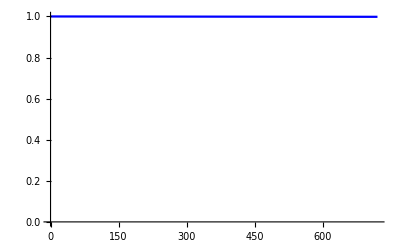

```mathematica
plot1m=ListLinePlot[prob1movr2y, PlotStyle->Blue, PlotRange->{0,1}]
```

```mathematica
probnoreinf3mtimecourse=Take[sarscov2probnoreinfectiontimecourse,90];
probnoreinf3m=Part[sarscov2probnoreinfectiontimecourse, 90];
prob3movr6y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,23]];
prob3movr2y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,7]];
```

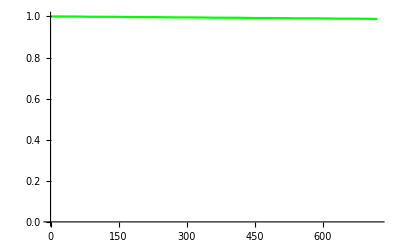

```mathematica
plot3m=ListLinePlot[prob3movr2y, PlotStyle->Green, PlotRange->{0,1}]
```

```mathematica
probnoreinf6mtimecourse=Take[sarscov2probnoreinfectiontimecourse,183];
probnoreinf6m=Part[sarscov2probnoreinfectiontimecourse, 183];
prob6movr6y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,11]];
prob6movr2y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,3]];
```

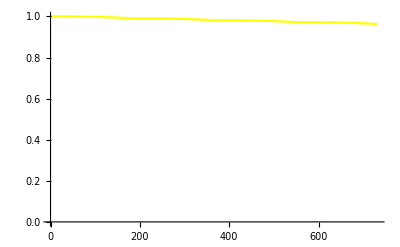

```mathematica
plot6m=ListLinePlot[prob6movr2y, PlotStyle->Yellow, PlotRange->{0,1}]
```

```mathematica
probnoreinf1ytimecourse=Take[sarscov2probnoreinfectiontimecourse,365];
probnoreinf1y=Part[sarscov2probnoreinfectiontimecourse, 365];
prob1yovr6y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,5]];
prob1yovr2y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,1]];
```

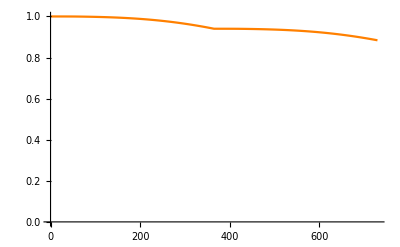

```mathematica
plot1y=ListLinePlot[prob1yovr2y, PlotStyle->Orange, PlotRange->{0,1}]
```

```mathematica
probnoreinf2ytimecourse=Take[sarscov2probnoreinfectiontimecourse,730];
probnoreinf2y=Part[sarscov2probnoreinfectiontimecourse, 730];
prob2yovr6y=Catenate[NestList[#*probnoreinf2y&,probnoreinf2ytimecourse,2]];
prob2yovr2y=Take[sarscov2probnoreinfectiontimecourse,730];
```

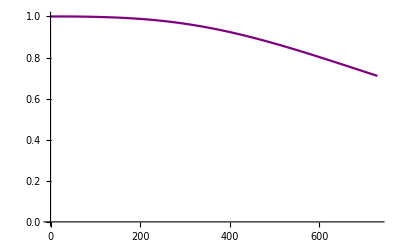

```mathematica
plot2y=ListLinePlot[prob2yovr2y, PlotStyle->Purple, PlotRange->{0,1}]
```

```mathematica
probnoreinf6ytimecourse=Take[sarscov2probnoreinfectiontimecourse,2190];
```

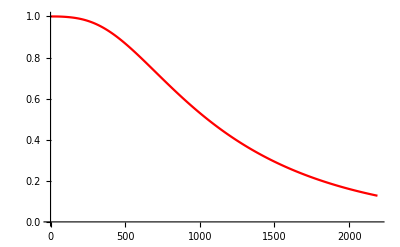

```mathematica
plot6y=ListLinePlot[probnoreinf6ytimecourse, PlotStyle->Red, PlotRange->{0,1}]
```

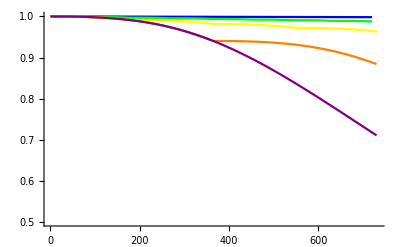

```mathematica
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1}]
```

```mathematica
Export[
StringJoin["/Users/hayley/Documents/townsend/spring-23/cancer/figs/no_cancer_boosterovrtime-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

/Users/hayley/Documents/townsend/spring-23/cancer/figs/no_cancer_boosterovrtime-by-Day_26Mar2024.pdf

```mathematica
Show[1-Last[prob2yovr2y], 1-Last[prob1yovr2y], 1-Last[prob6movr2y], 1-Last[prob3movr2y],1-Last[prob1movr2y]]
```

Show::gcomb: Could not combine the graphics objects in Show[0.289475,0.115999,0.0369396,0.0121525,0.00172878].

Show[0.289475,0.115999,0.0369396,0.0121525,0.00172878]

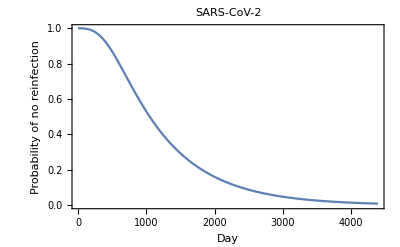

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
Export[
StringJoin["/Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_26Mar2024.pdf.

$Failed

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{10.7332,0.357773,0.029406}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1050.82,35.0274,2.87897}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2961.92,98.7308,8.11486}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<1201,
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

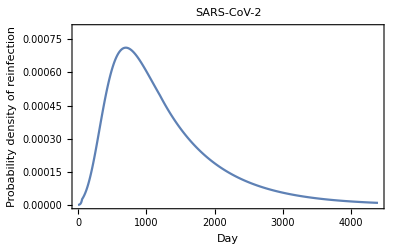

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0008},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0005},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_26Mar2024.pdf.

$Failed

# Boostertime - NY

Seasonality for the year in new york

```mathematica
year=2023;monthValues={{1,0.1826075431},{2,0.08742663136},{3,0.06618265855},{4,0.04422302067},{5,0.02420531657},{6,0.02938076547},{7,0.02938076547},{8,0.03162644416},{9,0.02938076547},{10,0.1442124894},{11,0.1893792909},{12,0.1419943088}};
nyseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.182608,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0874266,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.0661827,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.044223,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0242053,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0316264,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.0293808,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.144212,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.189379,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994,0.141994}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[nyseas365dtab]
nyseas365dtab=nyseas365dtab/meanValue;
```

0.0834119

Add rising booster data from https://www.nejm.org/doi/full/10.1056/NEJMoa2119451

```mathematica
waningpostboost=1-Take[sarscov2probnoreinfectiontimecourse,706];
```

```mathematica
risingpostboost={{0,{0.04992839056749099}},{7,{0.03249475891}},{14,{0.00628930818}},{24,{0}}}
```

{{0,{0.0499284}},{7,{0.0324948}},{14,{0.00628931}},{24,{0}}}

```mathematica
TableForm[risingpostboost]
```

0 | 0.0499284
7 | 0.0324948
14 | 0.00628931
24 | 0

Interpolate between days

```mathematica
risingpostboostint=Interpolation[risingpostboost, InterpolationOrder->1]
```

InterpolatingFunction[…]

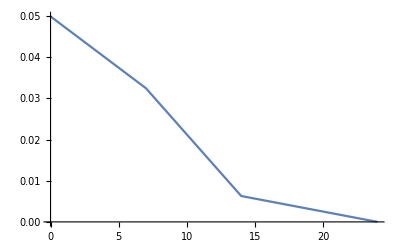

```mathematica
Plot[risingpostboostint[x],{x,0.,24.}]
```

```mathematica
risingpostboosttab={};
day=0;
While[0<=day<=24,
risingpostboosttab=Append[risingpostboosttab, risingpostboostint[day]];
risingpostboosttab=Flatten[risingpostboosttab];
Increment[day];
];
risingpostboosttab
```

{0.0499284,0.0474379,0.0449474,0.0424568,0.0399663,0.0374758,0.0349853,0.0324948,0.0287511,0.0250075,0.0212639,0.0175202,0.0137766,0.0100329,0.00628931,0.00566038,0.00503145,0.00440252,0.00377358,0.00314465,0.00251572,0.00188679,0.00125786,0.000628931,0.}

Append to beginning of booster data

```mathematica
postboost = Join[Take[risingpostboosttab, 24],waningpostboost];
postboost=Flatten[postboost];
postboost;
```

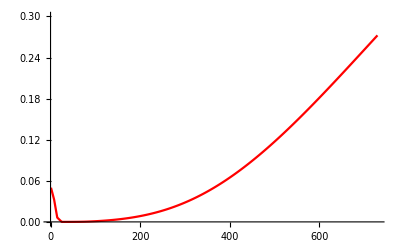

```mathematica
plotwaning=ListLinePlot[postboost, PlotStyle->Red, PlotRange->{0,0.3}]
```

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

259

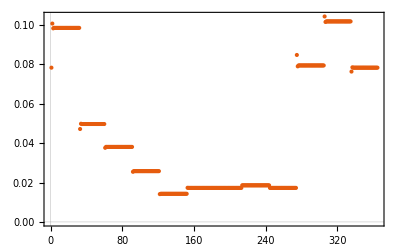

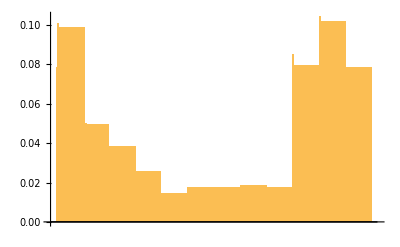

```mathematica
(*Assuming nyseas365dtab and postboost are defined*)(*Initialize arrays*)nyboost365=ConstantArray[0,365];
avgnyboost365=ConstantArray[0,365];
nydicty=Association[];

(*Process each day*)
Do[If[i==259,Print[i]];
currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*nyseas365dtab[[idx]]*postboost[[idx]],prev*nyseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[nyseas365dtab]]];
(*Update the dictionary and arrays*)nydicty[i]=1-currDays;
nyboost365[[i]]=Last[nydicty[i]];
avgnyboost365[[i]]=Mean[nydicty[i]];
nyseas365dtab=RotateLeft[nyseas365dtab],{i,Length[nyseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)

(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[nyboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
BarChart[nyboost365,ChartLabels->dates]
```

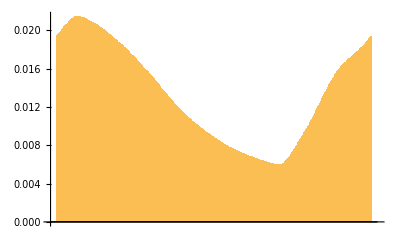

```mathematica
BarChart[avgnyboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgnyboost365.csv",avgnyboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgnyboost365.csv

```mathematica
minIndex=First@First@Position[avgnyboost365,Min[avgnyboost365]]
Min[avgnyboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

259

0.00598423

Index of minimum value: 259

Date corresponding to index: Fri 15 Sep 2023

```mathematica
maxIndex=First@First@Position[avgnyboost365,Max[avgnyboost365]]
Max[avgnyboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

25

0.0214612

Index of maximum value: 25

Date corresponding to index: Tue 24 Jan 2023

***HEAT MAP***

```mathematica
(*Assuming nyseas365dtab is defined,similar to postboost*)nyseas730dtab=Join[nyseas365dtab,nyseas365dtab];
nyboost730=ConstantArray[0,730];
nydicty=<||>;(*Use an association for dictionary functionality*)avgnyboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[nyseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*nyseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*nyseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
nydicty[i]=1-currDays;
(*Roll nyseas730dtab*)nyseas730dtab=RotateLeft[nyseas730dtab,1];
nyboost730[[i]]=Last[nydicty[i]];
avgnyboost730[[i]]=Mean[nydicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
nylist=Values[nydicty];
(*Assuming nydicty and avgnyboost365 are defined*)(*Convert dictionary to list-This part might be redundant if nylist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgnyboost365,Min[avgnyboost365]][[1,1]];(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
nystartBest=RotateList[nylist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*nystartBest=RotateList[nylist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*nystartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)nyheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[nystartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[nystartBest[[inf]],{1,Min[365-inf+boost,Length[nystartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[nystartBest[[boost]],{1,Min[365-boost,Length[nystartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
nyheat[[inf]]=norm;];

(*Rotate nyheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
nyheatt=Transpose[nyheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[nyheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,nyheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/ny_heat.csv",roundedListOfLists]
```

{181,358}

Thu 29 Jun 2023

Sat 23 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/ny_heat.csv

```mathematica
MatrixPlot[nyheatt,ColorFunction->(ColorData[{"Rainbow",{0.0001,0.1}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - stockholm

Seasonality for the year in stockholm

```mathematica
year=2023;monthValues={{1,0.173127709},{2,0.175483036},{3,0.156588709},{4,0.097399452},{5,0.062814518},{6,0.042391794},{7,0.013653416},{8,0.009724949},{9,0.011581329},{10,0.021626928},{11,0.059729648},{12,0.175878512}};
stockholmseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.173128,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.175483,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.156589,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0973995,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0628145,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0423918,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.0136534,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.00972495,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0115813,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0216269,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.0597296,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879,0.175879}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[stockholmseas365dtab]
stockholmseas365dtab=stockholmseas365dtab/meanValue;
```

0.0829108

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

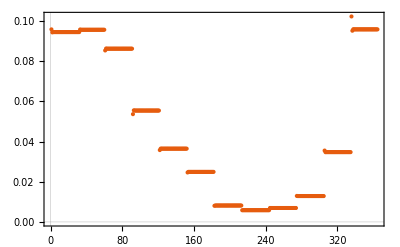

```mathematica
(*Assuming stockholmseas365dtab and postboost are defined*)(*Initialize arrays*)stockholmboost365=ConstantArray[0,365];
avgstockholmboost365=ConstantArray[0,365];
stockholmdicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*stockholmseas365dtab[[idx]]*postboost[[idx]],prev*stockholmseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[stockholmseas365dtab]]];
(*Update the dictionary and arrays*)stockholmdicty[i]=1-currDays;
stockholmboost365[[i]]=Last[stockholmdicty[i]];
avgstockholmboost365[[i]]=Mean[stockholmdicty[i]];
stockholmseas365dtab=RotateLeft[stockholmseas365dtab],{i,Length[stockholmseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[stockholmboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

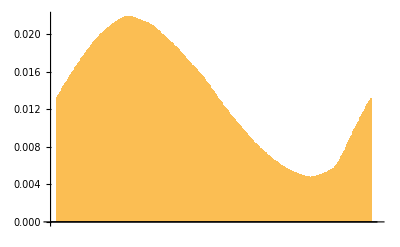

```mathematica
BarChart[avgstockholmboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgstockholmboost365.csv",avgstockholmboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgstockholmboost365.csv

```mathematica
minIndex=First@First@Position[avgstockholmboost365,Min[avgstockholmboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 295

Date corresponding to index: Sat 21 Oct 2023

```mathematica
maxIndex=First@First@Position[avgstockholmboost365,Max[avgstockholmboost365]]
Max[avgstockholmboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

83

0.0219043

Index of maximum value: 83

Date corresponding to index: Thu 23 Mar 2023

***HEAT MAP***

```mathematica
(*Assuming stockholmseas365dtab is defined,similar to postboost*)stockholmseas730dtab=Join[stockholmseas365dtab,stockholmseas365dtab];
stockholmboost730=ConstantArray[0,730];
stockholmdicty=<||>;(*Use an association for dictionary functionality*)avgstockholmboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[stockholmseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*stockholmseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*stockholmseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
stockholmdicty[i]=1-currDays;
(*Roll stockholmseas730dtab*)stockholmseas730dtab=RotateLeft[stockholmseas730dtab,1];
stockholmboost730[[i]]=Last[stockholmdicty[i]];
avgstockholmboost730[[i]]=Mean[stockholmdicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
stockholmlist=Values[stockholmdicty];
(*Assuming stockholmdicty and avgstockholmboost365 are defined*)(*Convert dictionary to list-This part might be redundant if stockholmlist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgstockholmboost365,Min[avgstockholmboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
stockholmstartBest=RotateList[stockholmlist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*stockholmstartBest=RotateList[stockholmlist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*stockholmstartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)stockholmheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[stockholmstartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[stockholmstartBest[[inf]],{1,Min[365-inf+boost,Length[stockholmstartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[stockholmstartBest[[boost]],{1,Min[365-boost,Length[stockholmstartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
stockholmheat[[inf]]=norm;];

(*Rotate stockholmheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
stockholmheatt=Transpose[stockholmheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[stockholmheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,stockholmheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/stockholm_heat.csv",roundedListOfLists]
```

{48,341}

Thu 16 Feb 2023

Wed 6 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/stockholm_heat.csv

```mathematica
MatrixPlot[stockholmheatt,ColorFunction->(ColorData[{"Rainbow",{0.0001,0.05}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - southkorea

Seasonality for the year in southkorea

```mathematica
year=2023;monthValues={{1,0.136529611},{2,0.095523842},{3,0.05407112},{4,0.055952553},{5,0.036247435},{6,0.029573814},{7,0.019419355},{8,0.0191948},{9,0.019821337},{10,0.067509217},{11,0.186960693},{12,0.279196222}};
southkoreaseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.13653,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0955238,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0540711,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0559526,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0362474,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0295738,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0194194,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0191948,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0198213,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.0675092,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.186961,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196,0.279196}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[southkoreaseas365dtab]
southkoreaseas365dtab=southkoreaseas365dtab/meanValue;
```

0.0833455

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

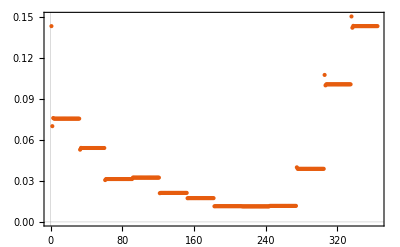

```mathematica
(*Assuming southkoreaseas365dtab and postboost are defined*)(*Initialize arrays*)southkoreaboost365=ConstantArray[0,365];
avgsouthkoreaboost365=ConstantArray[0,365];
southkoreadicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*southkoreaseas365dtab[[idx]]*postboost[[idx]],prev*southkoreaseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[southkoreaseas365dtab]]];
(*Update the dictionary and arrays*)southkoreadicty[i]=1-currDays;
southkoreaboost365[[i]]=Last[southkoreadicty[i]];
avgsouthkoreaboost365[[i]]=Mean[southkoreadicty[i]];
southkoreaseas365dtab=RotateLeft[southkoreaseas365dtab],{i,Length[southkoreaseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[southkoreaboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

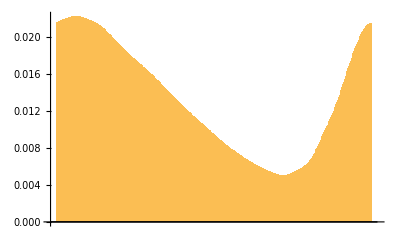

```mathematica
BarChart[avgsouthkoreaboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgsouthkoreaboost365.csv",avgsouthkoreaboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgsouthkoreaboost365.csv

```mathematica
minIndex=First@First@Position[avgsouthkoreaboost365,Min[avgsouthkoreaboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 263

Date corresponding to index: Tue 19 Sep 2023

```mathematica
maxIndex=First@First@Position[avgsouthkoreaboost365,Max[avgsouthkoreaboost365]]
Max[avgsouthkoreaboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

22

0.0222127

Index of maximum value: 22

Date corresponding to index: Sat 21 Jan 2023

***HEAT MAP***

```mathematica
(*Assuming southkoreaseas365dtab is defined,similar to postboost*)southkoreaseas730dtab=Join[southkoreaseas365dtab,southkoreaseas365dtab];
southkoreaboost730=ConstantArray[0,730];
southkoreadicty=<||>;(*Use an association for dictionary functionality*)avgsouthkoreaboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[southkoreaseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*southkoreaseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*southkoreaseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
southkoreadicty[i]=1-currDays;
(*Roll southkoreaseas730dtab*)southkoreaseas730dtab=RotateLeft[southkoreaseas730dtab,1];
southkoreaboost730[[i]]=Last[southkoreadicty[i]];
avgsouthkoreaboost730[[i]]=Mean[southkoreadicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
southkorealist=Values[southkoreadicty];
(*Assuming southkoreadicty and avgsouthkoreaboost365 are defined*)(*Convert dictionary to list-This part might be redundant if southkorealist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgsouthkoreaboost365,Min[avgsouthkoreaboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
southkoreastartBest=RotateList[southkorealist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*southkoreastartBest=RotateList[southkorealist,best+1];*)(*+1 for 1-based indexing adjustment*)(*southkoreastartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)southkoreaheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[southkoreastartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[southkoreastartBest[[inf]],{1,Min[365-inf+boost,Length[southkoreastartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[southkoreastartBest[[boost]],{1,Min[365-boost,Length[southkoreastartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
southkoreaheat[[inf]]=norm;];

(*Rotate southkoreaheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
southkoreaheatt=Transpose[southkoreaheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[southkoreaheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,southkoreaheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/southkorea_heat.csv",roundedListOfLists]
```

{181,365}

Thu 29 Jun 2023

Sat 30 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/southkorea_heat.csv

```mathematica
"/Users/hayley/Documents/townsend/spring_24/boostertime/figs/southkorea_heat.csv"
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/southkorea_heat.csv

```mathematica
lowheat=Min[Flatten[southkoreaheatt]]
highheat=Max[Flatten[southkoreaheatt]]
```

0.00260248

0.102488

```mathematica
MatrixPlot[southkoreaheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - edinburgh

Seasonality for the year in edinburgh

```mathematica
year=2023;monthValues={{1,0.110944222},{2,0.243398891},{3,0.145334359},{4,0.086148417},{5,0.050477925},{6,0.035530523},{7,0.005510476},{8,0.0000000000000213},{9,0.020370111},{10,0.038616897},{11,0.125348808},{12,0.138319373}};
edinburghseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.110944,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.243399,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.145334,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0861484,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0504779,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.0355305,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,0.00551048,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0203701,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.0386169,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.125349,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319,0.138319}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[edinburghseas365dtab]
edinburghseas365dtab=edinburghseas365dtab/meanValue;
```

0.0821984

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

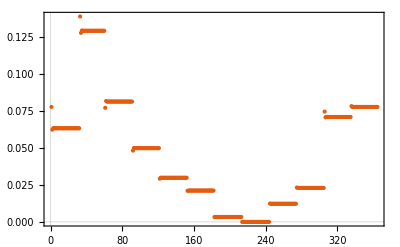

```mathematica
(*Assuming edinburghseas365dtab and postboost are defined*)(*Initialize arrays*)edinburghboost365=ConstantArray[0,365];
avgedinburghboost365=ConstantArray[0,365];
edinburghdicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*edinburghseas365dtab[[idx]]*postboost[[idx]],prev*edinburghseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[edinburghseas365dtab]]];
(*Update the dictionary and arrays*)edinburghdicty[i]=1-currDays;
edinburghboost365[[i]]=Last[edinburghdicty[i]];
avgedinburghboost365[[i]]=Mean[edinburghdicty[i]];
edinburghseas365dtab=RotateLeft[edinburghseas365dtab],{i,Length[edinburghseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[edinburghboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

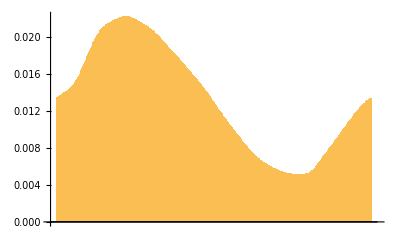

```mathematica
BarChart[avgedinburghboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgedinburghboost365.csv",avgedinburghboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgedinburghboost365.csv

```mathematica
minIndex=First@First@Position[avgedinburghboost365,Min[avgedinburghboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 283

Date corresponding to index: Mon 9 Oct 2023

```mathematica
maxIndex=First@First@Position[avgedinburghboost365,Max[avgedinburghboost365]]
Max[avgedinburghboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

80

0.0222637

Index of maximum value: 80

Date corresponding to index: Mon 20 Mar 2023

***HEAT MAP***

```mathematica
(*Assuming edinburghseas365dtab is defined,similar to postboost*)edinburghseas730dtab=Join[edinburghseas365dtab,edinburghseas365dtab];
edinburghboost730=ConstantArray[0,730];
edinburghdicty=<||>;(*Use an association for dictionary functionality*)avgedinburghboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[edinburghseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*edinburghseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*edinburghseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
edinburghdicty[i]=1-currDays;
(*Roll edinburghseas730dtab*)edinburghseas730dtab=RotateLeft[edinburghseas730dtab,1];
edinburghboost730[[i]]=Last[edinburghdicty[i]];
avgedinburghboost730[[i]]=Mean[edinburghdicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
edinburghlist=Values[edinburghdicty];
(*Assuming edinburghdicty and avgedinburghboost365 are defined*)(*Convert dictionary to list-This part might be redundant if edinburghlist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgedinburghboost365,Min[avgedinburghboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
edinburghstartBest=RotateList[edinburghlist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*edinburghstartBest=RotateList[edinburghlist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*edinburghstartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)edinburghheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[edinburghstartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[edinburghstartBest[[inf]],{1,Min[365-inf+boost,Length[edinburghstartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[edinburghstartBest[[boost]],{1,Min[365-boost,Length[edinburghstartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
edinburghheat[[inf]]=norm;];

(*Rotate edinburghheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
edinburghheatt=Transpose[edinburghheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[edinburghheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,edinburghheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/edinburgh_heat.csv",roundedListOfLists]
```

{102,349}

Tue 11 Apr 2023

Thu 14 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/edinburgh_heat.csv

```mathematica
lowheat=Min[Flatten[edinburghheatt]]
highheat=Max[Flatten[edinburghheatt]]
```

0.00265044

0.0996202

```mathematica
MatrixPlot[edinburghheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - yamagata

Seasonality for the year in yamagata

```mathematica
year=2023;monthValues={{1,0.166013252},{2,0.231966326},{3,0.177662275},{4,0.081456534},{5,0.055383917},{6,0.019746716},{7,0.046355124},{8,0.025981733},{9,0.019267389},{10,0.043361622},{11,0.075619074},{12,0.057186038}};
yamagataseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.166013,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.231966,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.177662,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0814565,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0553839,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0197467,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0463551,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0259817,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0192674,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0433616,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.0756191,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186,0.057186}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[yamagataseas365dtab]
yamagataseas365dtab=yamagataseas365dtab/meanValue;
```

0.0824877

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

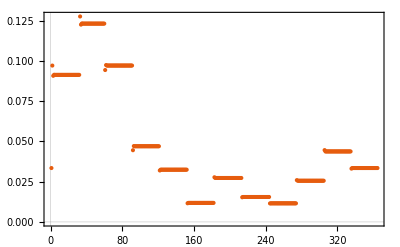

```mathematica
(*Assuming yamagataseas365dtab and postboost are defined*)(*Initialize arrays*)yamagataboost365=ConstantArray[0,365];
avgyamagataboost365=ConstantArray[0,365];
yamagatadicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*yamagataseas365dtab[[idx]]*postboost[[idx]],prev*yamagataseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[yamagataseas365dtab]]];
(*Update the dictionary and arrays*)yamagatadicty[i]=1-currDays;
yamagataboost365[[i]]=Last[yamagatadicty[i]];
avgyamagataboost365[[i]]=Mean[yamagatadicty[i]];
yamagataseas365dtab=RotateLeft[yamagataseas365dtab],{i,Length[yamagataseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[yamagataboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

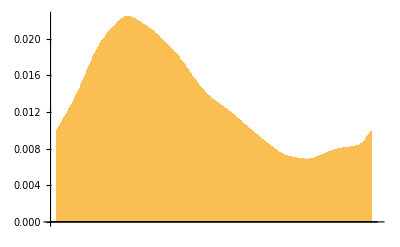

```mathematica
BarChart[avgyamagataboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgyamagataboost365.csv",avgyamagataboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgyamagataboost365.csv

```mathematica
minIndex=First@First@Position[avgyamagataboost365,Min[avgyamagataboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 292

Date corresponding to index: Wed 18 Oct 2023

```mathematica
maxIndex=First@First@Position[avgyamagataboost365,Max[avgyamagataboost365]]
Max[avgyamagataboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

83

0.022418

Index of maximum value: 83

Date corresponding to index: Thu 23 Mar 2023

***HEAT MAP***

```mathematica
(*Assuming yamagataseas365dtab is defined,similar to postboost*)yamagataseas730dtab=Join[yamagataseas365dtab,yamagataseas365dtab];
yamagataboost730=ConstantArray[0,730];
yamagatadicty=<||>;(*Use an association for dictionary functionality*)avgyamagataboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[yamagataseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*yamagataseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*yamagataseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
yamagatadicty[i]=1-currDays;
(*Roll yamagataseas730dtab*)yamagataseas730dtab=RotateLeft[yamagataseas730dtab,1];
yamagataboost730[[i]]=Last[yamagatadicty[i]];
avgyamagataboost730[[i]]=Mean[yamagatadicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
yamagatalist=Values[yamagatadicty];
(*Assuming yamagatadicty and avgyamagataboost365 are defined*)(*Convert dictionary to list-This part might be redundant if yamagatalist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgyamagataboost365,Min[avgyamagataboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
yamagatastartBest=RotateList[yamagatalist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*yamagatastartBest=RotateList[yamagatalist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*yamagatastartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)yamagataheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[yamagatastartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[yamagatastartBest[[inf]],{1,Min[365-inf+boost,Length[yamagatastartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[yamagatastartBest[[boost]],{1,Min[365-boost,Length[yamagatastartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
yamagataheat[[inf]]=norm;];

(*Rotate yamagataheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
yamagataheatt=Transpose[yamagataheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[yamagataheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,yamagataheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/yamagata_heat.csv",roundedListOfLists]
```

{78,343}

Sat 18 Mar 2023

Fri 8 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/yamagata_heat.csv

```mathematica
lowheat=Min[Flatten[yamagataheatt]]
highheat=Max[Flatten[yamagataheatt]]
```

0.00295187

0.108331

```mathematica
MatrixPlot[yamagataheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - nepal

Seasonality for the year in nepal

```mathematica
year=2023;monthValues={{1,0.149929627},{2,0.19655469},{3,0.088084475},{4,0.055980264},{5,0.08557618},{6,0.061443946},{7,0.021400864},{8,0.047174294},{9,0.064715711},{10,0.073773821},{11,0.081789807},{12,0.073576319}};
nepalseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.14993,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.196555,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0880845,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0559803,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0855762,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0614439,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0214009,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0471743,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0647157,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0737738,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0817898,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763,0.0735763}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[nepalseas365dtab]
nepalseas365dtab=nepalseas365dtab/meanValue;
```

0.0825929

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

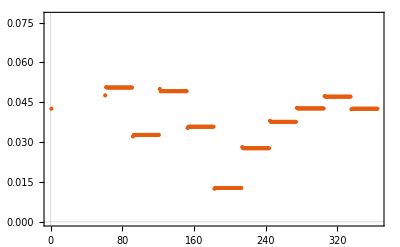

```mathematica
(*Assuming nepalseas365dtab and postboost are defined*)(*Initialize arrays*)nepalboost365=ConstantArray[0,365];
avgnepalboost365=ConstantArray[0,365];
nepaldicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*nepalseas365dtab[[idx]]*postboost[[idx]],prev*nepalseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[nepalseas365dtab]]];
(*Update the dictionary and arrays*)nepaldicty[i]=1-currDays;
nepalboost365[[i]]=Last[nepaldicty[i]];
avgnepalboost365[[i]]=Mean[nepaldicty[i]];
nepalseas365dtab=RotateLeft[nepalseas365dtab],{i,Length[nepalseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[nepalboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

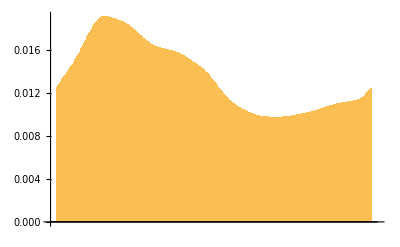

```mathematica
BarChart[avgnepalboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgnepalboost365.csv",avgnepalboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgnepalboost365.csv

```mathematica
minIndex=First@First@Position[avgnepalboost365,Min[avgnepalboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 255

Date corresponding to index: Mon 11 Sep 2023

```mathematica
maxIndex=First@First@Position[avgnepalboost365,Max[avgnepalboost365]]
Max[avgnepalboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

56

0.0190845

Index of maximum value: 56

Date corresponding to index: Fri 24 Feb 2023

***HEAT MAP***

```mathematica
(*Assuming nepalseas365dtab is defined,similar to postboost*)nepalseas730dtab=Join[nepalseas365dtab,nepalseas365dtab];
nepalboost730=ConstantArray[0,730];
nepaldicty=<||>;(*Use an association for dictionary functionality*)avgnepalboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[nepalseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*nepalseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*nepalseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
nepaldicty[i]=1-currDays;
(*Roll nepalseas730dtab*)nepalseas730dtab=RotateLeft[nepalseas730dtab,1];
nepalboost730[[i]]=Last[nepaldicty[i]];
avgnepalboost730[[i]]=Mean[nepaldicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
nepallist=Values[nepaldicty];
(*Assuming nepaldicty and avgnepalboost365 are defined*)(*Convert dictionary to list-This part might be redundant if nepallist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgnepalboost365,Min[avgnepalboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
nepalstartBest=RotateList[nepallist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*nepalstartBest=RotateList[nepallist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*nepalstartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)nepalheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[nepalstartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[nepalstartBest[[inf]],{1,Min[365-inf+boost,Length[nepalstartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[nepalstartBest[[boost]],{1,Min[365-boost,Length[nepalstartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
nepalheat[[inf]]=norm;];

(*Rotate nepalheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
nepalheatt=Transpose[nepalheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[nepalheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,nepalheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/nepal_heat.csv",roundedListOfLists]
```

{109,345}

Tue 18 Apr 2023

Sun 10 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/nepal_heat.csv

```mathematica
lowheat=Min[Flatten[nepalheatt]]
highheat=Max[Flatten[nepalheatt]]
```

0.00321456

0.118102

```mathematica
MatrixPlot[nepalheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - guangzhou

Seasonality for the year in guangzhou

```mathematica
year=2023;monthValues={{1,0.149147579},{2,0.167449489},{3,0.105426513},{4,0.085655396},{5,0.042971861},{6,0.032977555},{7,0.026251653},{8,0.017009778},{9,0.024545628},{10,0.040325556},{11,0.130609834},{12,0.177629159}};
guangzhouseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[guangzhouseas365dtab]
guangzhouseas365dtab=guangzhouseas365dtab/meanValue;
```

0.0828051

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

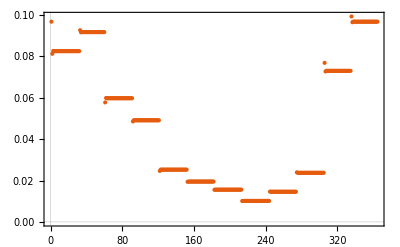

```mathematica
(*Assuming guangzhouseas365dtab and postboost are defined*)(*Initialize arrays*)guangzhouboost365=ConstantArray[0,365];
avgguangzhouboost365=ConstantArray[0,365];
guangzhoudicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*guangzhouseas365dtab[[idx]]*postboost[[idx]],prev*guangzhouseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[guangzhouseas365dtab]]];
(*Update the dictionary and arrays*)guangzhoudicty[i]=1-currDays;
guangzhouboost365[[i]]=Last[guangzhoudicty[i]];
avgguangzhouboost365[[i]]=Mean[guangzhoudicty[i]];
guangzhouseas365dtab=RotateLeft[guangzhouseas365dtab],{i,Length[guangzhouseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[guangzhouboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

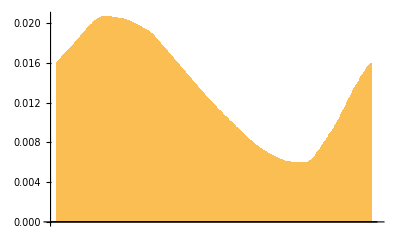

```mathematica
BarChart[avgguangzhouboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgguangzhouboost365.csv",avgguangzhouboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgguangzhouboost365.csv

```mathematica
minIndex=First@First@Position[avgguangzhouboost365,Min[avgguangzhouboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 284

Date corresponding to index: Tue 10 Oct 2023

```mathematica
maxIndex=First@First@Position[avgguangzhouboost365,Max[avgguangzhouboost365]]
Max[avgguangzhouboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

57

0.0206841

Index of maximum value: 57

Date corresponding to index: Sat 25 Feb 2023

***HEAT MAP***

```mathematica
(*Assuming guangzhouseas365dtab is defined,similar to postboost*)guangzhouseas730dtab=Join[guangzhouseas365dtab,guangzhouseas365dtab];
guangzhouboost730=ConstantArray[0,730];
guangzhoudicty=<||>;(*Use an association for dictionary functionality*)avgguangzhouboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[guangzhouseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*guangzhouseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*guangzhouseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
guangzhoudicty[i]=1-currDays;
(*Roll guangzhouseas730dtab*)guangzhouseas730dtab=RotateLeft[guangzhouseas730dtab,1];
guangzhouboost730[[i]]=Last[guangzhoudicty[i]];
avgguangzhouboost730[[i]]=Mean[guangzhoudicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
guangzhoulist=Values[guangzhoudicty];
(*Assuming guangzhoudicty and avgguangzhouboost365 are defined*)(*Convert dictionary to list-This part might be redundant if guangzhoulist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgguangzhouboost365,Min[avgguangzhouboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
guangzhoustartBest=RotateList[guangzhoulist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*guangzhoustartBest=RotateList[guangzhoulist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*guangzhoustartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)guangzhouheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[guangzhoustartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[guangzhoustartBest[[inf]],{1,Min[365-inf+boost,Length[guangzhoustartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[guangzhoustartBest[[boost]],{1,Min[365-boost,Length[guangzhoustartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
guangzhouheat[[inf]]=norm;];

(*Rotate guangzhouheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
guangzhouheatt=Transpose[guangzhouheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[guangzhouheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,guangzhouheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/guangzhou_heat.csv",roundedListOfLists]
```

{151,354}

Tue 30 May 2023

Tue 19 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/guangzhou_heat.csv

```mathematica
lowheat=Min[Flatten[guangzhouheatt]]
highheat=Max[Flatten[guangzhouheatt]]
```

0.0030735

0.103623

```mathematica
MatrixPlot[guangzhouheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - norway

Seasonality for the year in norway

```mathematica
year=2023;monthValues={{1,0.149147579},{2,0.167449489},{3,0.105426513},{4,0.085655396},{5,0.042971861},{6,0.032977555},{7,0.026251653},{8,0.017009778},{9,0.024545628},{10,0.040325556},{11,0.130609834},{12,0.177629159}};
norwayseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.149148,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.167449,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.105427,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0856554,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0429719,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0329776,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0262517,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0170098,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0245456,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.0403256,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.13061,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629,0.177629}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[norwayseas365dtab]
norwayseas365dtab=norwayseas365dtab/meanValue;
```

0.0828051

Add rising booster data from https://www.nejm.org/doi/full/10.1056/NEJMoa2119451

```mathematica
waningpostboost=1-Take[sarscov2probnoreinfectiontimecourse,706];
```

```mathematica
risingpostboost={{0,{0.04992839056749099}},{7,{0.03249475891}},{14,{0.00628930818}},{24,{0}}}
```

{{0,{0.0499284}},{7,{0.0324948}},{14,{0.00628931}},{24,{0}}}

```mathematica
TableForm[risingpostboost]
```

0 | 0.0499284
7 | 0.0324948
14 | 0.00628931
24 | 0

Interpolate between days

```mathematica
risingpostboostint=Interpolation[risingpostboost, InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Plot[risingpostboostint[x],{x,0.,24.}]
```

-Graphics-

```mathematica
risingpostboosttab={};
day=0;
While[0<=day<=24,
risingpostboosttab=Append[risingpostboosttab, risingpostboostint[day]];
risingpostboosttab=Flatten[risingpostboosttab];
Increment[day];
];
risingpostboosttab
```

{0.0499284,0.0474379,0.0449474,0.0424568,0.0399663,0.0374758,0.0349853,0.0324948,0.0287511,0.0250075,0.0212639,0.0175202,0.0137766,0.0100329,0.00628931,0.00566038,0.00503145,0.00440252,0.00377358,0.00314465,0.00251572,0.00188679,0.00125786,0.000628931,0.}

Append to beginning of booster data

```mathematica
postboost = Join[Take[risingpostboosttab, 24],waningpostboost];
postboost=Flatten[postboost];
postboost;
```

```mathematica
plotwaning=ListLinePlot[postboost, PlotStyle->Red, PlotRange->{0,0.3}]
```

-Graphics-

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

```mathematica
(*Assuming norwayseas365dtab and postboost are defined*)(*Initialize arrays*)norwayboost365=ConstantArray[0,365];
avgnorwayboost365=ConstantArray[0,365];
norwaydicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*norwayseas365dtab[[idx]]*postboost[[idx]],prev*norwayseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[norwayseas365dtab]]];
(*Update the dictionary and arrays*)norwaydicty[i]=1-currDays;
norwayboost365[[i]]=Last[norwaydicty[i]];
avgnorwayboost365[[i]]=Mean[norwaydicty[i]];
norwayseas365dtab=RotateLeft[norwayseas365dtab],{i,Length[norwayseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[norwayboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

-Graphics-

```mathematica
BarChart[avgnorwayboost365,ChartLabels->dates]
```

-Graphics-

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgnorwayboost365.csv",avgnorwayboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgnorwayboost365.csv

```mathematica
minIndex=First@First@Position[avgnorwayboost365,Min[avgnorwayboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 284

Date corresponding to index: Tue 10 Oct 2023

```mathematica
maxIndex=First@First@Position[avgnorwayboost365,Max[avgnorwayboost365]]
Max[avgnorwayboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

57

0.0206841

Index of maximum value: 57

Date corresponding to index: Sat 25 Feb 2023

***HEAT MAP***

```mathematica
(*Assuming norwayseas365dtab is defined,similar to postboost*)norwayseas730dtab=Join[norwayseas365dtab,norwayseas365dtab];
norwayboost730=ConstantArray[0,730];
norwaydicty=<||>;(*Use an association for dictionary functionality*)avgnorwayboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[norwayseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*norwayseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*norwayseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
norwaydicty[i]=1-currDays;
(*Roll norwayseas730dtab*)norwayseas730dtab=RotateLeft[norwayseas730dtab,1];
norwayboost730[[i]]=Last[norwaydicty[i]];
avgnorwayboost730[[i]]=Mean[norwaydicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
norwaylist=Values[norwaydicty];
(*Assuming norwaydicty and avgnorwayboost365 are defined*)(*Convert dictionary to list-This part might be redundant if norwaylist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgnorwayboost365,Min[avgnorwayboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
norwaystartBest=RotateList[norwaylist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*norwaystartBest=RotateList[norwaylist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*norwaystartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)norwayheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[norwaystartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[norwaystartBest[[inf]],{1,Min[365-inf+boost,Length[norwaystartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[norwaystartBest[[boost]],{1,Min[365-boost,Length[norwaystartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
norwayheat[[inf]]=norm;];

(*Rotate norwayheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
norwayheatt=Transpose[norwayheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[norwayheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,norwayheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/norway_heat.csv",roundedListOfLists]
```

{151,354}

Tue 30 May 2023

Tue 19 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/norway_heat.csv

```mathematica
lowheat=Min[Flatten[norwayheatt]]
highheat=Max[Flatten[norwayheatt]]
```

0.0030735

0.103623

```mathematica
MatrixPlot[norwayheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - netherlands

Seasonality for the year in netherlands

```mathematica
year=2023;monthValues={{1,0.103649095},{2,0.117290268},{3,0.114495525},{4,0.105698381},{5,0.099480428},{6,0.071252356},{7,0.056980989},{8,0.054372522},{9,0.047332347},{10,0.064559454},{11,0.072722296},{12,0.102923007}};
netherlandsseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[netherlandsseas365dtab]
netherlandsseas365dtab=netherlandsseas365dtab/meanValue;
```

0.0840673

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

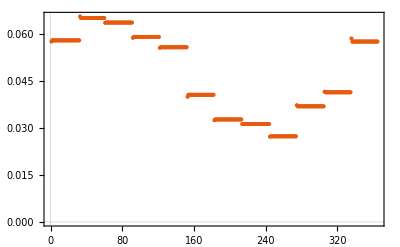

```mathematica
(*Assuming netherlandsseas365dtab and postboost are defined*)(*Initialize arrays*)netherlandsboost365=ConstantArray[0,365];
avgnetherlandsboost365=ConstantArray[0,365];
netherlandsdicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*netherlandsseas365dtab[[idx]]*postboost[[idx]],prev*netherlandsseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[netherlandsseas365dtab]]];
(*Update the dictionary and arrays*)netherlandsdicty[i]=1-currDays;
netherlandsboost365[[i]]=Last[netherlandsdicty[i]];
avgnetherlandsboost365[[i]]=Mean[netherlandsdicty[i]];
netherlandsseas365dtab=RotateLeft[netherlandsseas365dtab],{i,Length[netherlandsseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[netherlandsboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

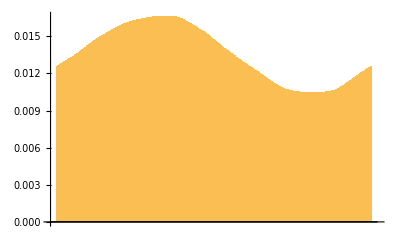

```mathematica
BarChart[avgnetherlandsboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgnetherlandsboost365.csv",avgnetherlandsboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgnetherlandsboost365.csv

```mathematica
minIndex=First@First@Position[avgnetherlandsboost365,Min[avgnetherlandsboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 296

Date corresponding to index: Sun 22 Oct 2023

```mathematica
maxIndex=First@First@Position[avgnetherlandsboost365,Max[avgnetherlandsboost365]]
Max[avgnetherlandsboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

128

0.0166096

Index of maximum value: 128

Date corresponding to index: Sun 7 May 2023

***HEAT MAP***

```mathematica
(*Assuming netherlandsseas365dtab is defined,similar to postboost*)netherlandsseas730dtab=Join[netherlandsseas365dtab,netherlandsseas365dtab];
netherlandsboost730=ConstantArray[0,730];
netherlandsdicty=<||>;(*Use an association for dictionary functionality*)avgnetherlandsboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[netherlandsseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*netherlandsseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*netherlandsseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
netherlandsdicty[i]=1-currDays;
(*Roll netherlandsseas730dtab*)netherlandsseas730dtab=RotateLeft[netherlandsseas730dtab,1];
netherlandsboost730[[i]]=Last[netherlandsdicty[i]];
avgnetherlandsboost730[[i]]=Mean[netherlandsdicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
netherlandslist=Values[netherlandsdicty];
(*Assuming netherlandsdicty and avgnetherlandsboost365 are defined*)(*Convert dictionary to list-This part might be redundant if netherlandslist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgnetherlandsboost365,Min[avgnetherlandsboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
netherlandsstartBest=RotateList[netherlandslist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*netherlandsstartBest=RotateList[netherlandslist,best+1];*)(*+1 for 1-based indexing adjustment*)(*netherlandsstartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)netherlandsheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[netherlandsstartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[netherlandsstartBest[[inf]],{1,Min[365-inf+boost,Length[netherlandsstartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[netherlandsstartBest[[boost]],{1,Min[365-boost,Length[netherlandsstartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
netherlandsheat[[inf]]=norm;];

(*Rotate netherlandsheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
netherlandsheatt=Transpose[netherlandsheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[netherlandsheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,netherlandsheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/netherlands_heat.csv",roundedListOfLists]
```

{153,351}

Thu 1 Jun 2023

Sat 16 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/netherlands_heat.csv

```mathematica
lowheat=Min[Flatten[netherlandsheatt]]
highheat=Max[Flatten[netherlandsheatt]]
```

0.00342396

0.122307

```mathematica
MatrixPlot[netherlandsheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```

# Boostertime - sweden (gothenburg)

Seasonality for the year in sweden (gothenburg)

```mathematica
year=2023;monthValues={{1,0.186305735},{2,0.194463996},{3,0.1132092},{4,0.054289347},{5,0.060163872},{6,0.067718763},{7,0.02821739},{8,0.026294091},{9,0.020989262},{10,0.061606261},{11,0.034528262},{12,0.15221382}};
swedenseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}];
```

{0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.186306,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.194464,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.113209,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0542893,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0601639,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0677188,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0282174,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0262941,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0209893,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0616063,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.0345283,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214,0.152214}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[swedenseas365dtab]
swedenseas365dtab=swedenseas365dtab/meanValue;
```

0.0828468

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

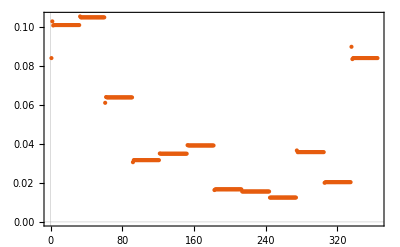

```mathematica
(*Assuming swedenseas365dtab and postboost are defined*)(*Initialize arrays*)swedenboost365=ConstantArray[0,365];
avgswedenboost365=ConstantArray[0,365];
swedendicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*swedenseas365dtab[[idx]]*postboost[[idx]],prev*swedenseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[swedenseas365dtab]]];
(*Update the dictionary and arrays*)swedendicty[i]=1-currDays;
swedenboost365[[i]]=Last[swedendicty[i]];
avgswedenboost365[[i]]=Mean[swedendicty[i]];
swedenseas365dtab=RotateLeft[swedenseas365dtab],{i,Length[swedenseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[swedenboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

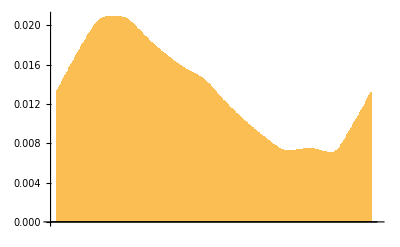

```mathematica
BarChart[avgswedenboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgswedenboost365.csv",avgswedenboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgswedenboost365.csv

```mathematica
minIndex=First@First@Position[avgswedenboost365,Min[avgswedenboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 319

Date corresponding to index: Tue 14 Nov 2023

```mathematica
maxIndex=First@First@Position[avgswedenboost365,Max[avgswedenboost365]]
Max[avgswedenboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

68

0.0209174

Index of maximum value: 68

Date corresponding to index: Wed 8 Mar 2023

***HEAT MAP***

```mathematica
(*Assuming swedenseas365dtab is defined,similar to postboost*)swedenseas730dtab=Join[swedenseas365dtab,swedenseas365dtab];
swedenboost730=ConstantArray[0,730];
swedendicty=<||>;(*Use an association for dictionary functionality*)avgswedenboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[swedenseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*swedenseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*swedenseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
swedendicty[i]=1-currDays;
(*Roll swedenseas730dtab*)swedenseas730dtab=RotateLeft[swedenseas730dtab,1];
swedenboost730[[i]]=Last[swedendicty[i]];
avgswedenboost730[[i]]=Mean[swedendicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
swedenlist=Values[swedendicty];
(*Assuming swedendicty and avgswedenboost365 are defined*)(*Convert dictionary to list-This part might be redundant if swedenlist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgswedenboost365,Min[avgswedenboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
swedenstartBest=RotateList[swedenlist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*swedenstartBest=RotateList[swedenlist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*swedenstartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)swedenheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[swedenstartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[swedenstartBest[[inf]],{1,Min[365-inf+boost,Length[swedenstartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[swedenstartBest[[boost]],{1,Min[365-boost,Length[swedenstartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
swedenheat[[inf]]=norm;];

(*Rotate swedenheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
swedenheatt=Transpose[swedenheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[swedenheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,swedenheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/sweden_heat.csv",roundedListOfLists]
```

{165,355}

Tue 13 Jun 2023

Wed 20 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/sweden_heat.csv

```mathematica
lowheat=Min[Flatten[swedenheatt]]
highheat=Max[Flatten[swedenheatt]]
```

0.00248609

0.106317

```mathematica
MatrixPlot[swedenheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic]
```

-Graphics-

# Boostertime - israel

Seasonality for the year in israel

```mathematica
year=2023;monthValues={{1,0.04992113},{2,0.0000000000000213},{3,0.107888511},{4,0.096738731},{5,0.168784906},{6,0.044958143},{7,0.013492959},{8,0.157287341},{9,0.048883072},{10,0.078962413},{11,0.137186214},{12,0.09589658}};
israelseas365dtab=Flatten@Table[Table[monthValues[[m,2]],{day,1,DayCount[{year,m,1},{year,m+1,1}]}],{m,1,12}]
```

{0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,0.0499211,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,2.13×10^-14,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.107889,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.0967387,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.168785,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.0449581,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.013493,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.157287,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0488831,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.0789624,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.137186,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966,0.0958966}

Divide by mean seasonality for the year

```mathematica
meanValue=Mean[israelseas365dtab]
israelseas365dtab=israelseas365dtab/meanValue;
```

0.0840335

Roll through days in the year, multiplying each day by booster probabilities, taking the inverse of those values, and then the product of those values

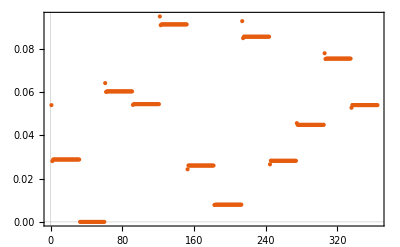

```mathematica
(*Assuming israelseas365dtab and postboost are defined*)(*Initialize arrays*)israelboost365=ConstantArray[0,365];
avgisraelboost365=ConstantArray[0,365];
israeldicty=Association[];

(*Process each day*)
Do[currDays=FoldList[(*This lambda function replaces the conditional inside the loop*)Function[{prev,idx},1-If[idx==1,(1-Last[postboost])*israelseas365dtab[[idx]]*postboost[[idx]],prev*israelseas365dtab[[idx]]*postboost[[idx]]]],1,Range[Length[israelseas365dtab]]];
(*Update the dictionary and arrays*)israeldicty[i]=1-currDays;
israelboost365[[i]]=Last[israeldicty[i]];
avgisraelboost365[[i]]=Mean[israeldicty[i]];
israelseas365dtab=RotateLeft[israelseas365dtab],{i,Length[israelseas365dtab]}];

(*Plotting and exporting,streamlined for readability*)



(*For plotting,assume `data` is prepared appropriately*)
(*Example of a simple plot*)
ListPlot[israelboost365,PlotTheme->"Scientific"]

(*For a bar chart with dates,assuming `dates` is a list of corresponding dates*)
(*Convert `dates` to Mathematica's date format if necessary*)
```

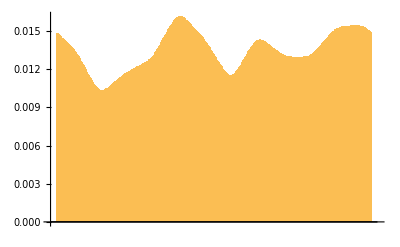

```mathematica
BarChart[avgisraelboost365,ChartLabels->dates]
```

```mathematica
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgisraelboost365.csv",avgisraelboost365]
```

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/avgisraelboost365.csv

```mathematica
minIndex=First@First@Position[avgisraelboost365,Min[avgisraelboost365]];

(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,minIndex-1];

(*Print the results*)
Print["Index of minimum value: ",minIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

Index of minimum value: 53

Date corresponding to index: Tue 21 Feb 2023

```mathematica
maxIndex=First@First@Position[avgisraelboost365,Max[avgisraelboost365]]
Max[avgisraelboost365]
(*Convert index to a date,starting from January 1st of a specific year*)
yearStart=DateObject[{2023,1,0}];(*Change the year as needed*)dateCorrespondingToIndex=DatePlus[yearStart,maxIndex-1];

(*Print the results*)
Print["Index of maximum value: ",maxIndex];
Print["Date corresponding to index: ",dateCorrespondingToIndex];
```

144

0.0161508

Index of maximum value: 144

Date corresponding to index: Tue 23 May 2023

***HEAT MAP***

```mathematica
(*Assuming israelseas365dtab is defined,similar to postboost*)israelseas730dtab=Join[israelseas365dtab,israelseas365dtab];
israelboost730=ConstantArray[0,730];
israeldicty=<||>;(*Use an association for dictionary functionality*)avgisraelboost730=ConstantArray[0,730];

(*Iterate through each booster day in a year*)
For[i=1,i<=365,i++,currDays={};
(*Iterate through each day in the year for a specific booster day*)For[t=1,t<=Length[israelseas730dtab],t++,If[t==1,(*First day,you don't take into account the previous day*)currDay=1-((1-0.0499284)*israelseas730dtab[[t]]*postboost[[t]]),(*Multiply seasonality by reinfection prob and by previous day*)currDay=1-(Last[currDays]*israelseas730dtab[[t]]*postboost[[t]])];
AppendTo[currDays,currDay];];
israeldicty[i]=1-currDays;
(*Roll israelseas730dtab*)israelseas730dtab=RotateLeft[israelseas730dtab,1];
israelboost730[[i]]=Last[israeldicty[i]];
avgisraelboost730[[i]]=Mean[israeldicty[i]];];

(*Convert the dictionary to a list if needed.For Mathematica,association keys can be directly used for iteration or data manipulation.*)
israellist=Values[israeldicty];
(*Assuming israeldicty and avgisraelboost365 are defined*)(*Convert dictionary to list-This part might be redundant if israellist is already defined as shown in the previous code conversion*)

(*Finding the best date for boosting*)
best=Position[avgisraelboost365,Min[avgisraelboost365]][[1,1]];
(*Adjusted for 0-based index emulation*)(*Define a rotate function similar to Python's*)RotateList[l_,n_]:=Join[Drop[l,n],Take[l,n]];

(*Start graphing at the first day of the month for the best date*)
bestMonthStart=Which[0<=best<=30,0,31<=best<=58,31,59<=best<=89,59,90<=best<=119,90,119<=best<=150,119,151<=best<=180,151,181<=best<=211,181,212<=best<=242,212,243<=best<=272,243,273<=best<=303,273,304<=best<=333,304,334<=best<=364,335];

(*Start at best date or month start,depending on your requirements*)
(*For starting at the best month start*)
israelstartBest=RotateList[israellist,bestMonthStart+1];(*+1 for 1-based indexing*)

(*For starting at the best date directly*)
(*israelstartBest=RotateList[israellist,best+1];*)
(*+1 for 1-based indexing adjustment*)(*israelstartBest now contains the rotated list starting from the best date or month start*)
```

```mathematica
(*Initialize the matrix to store normalized values for each infection and booster combination*)israelheat=ConstantArray[0,{365,365}];

(*Iterate for an infection happening between the best date to best date*)
For[inf=1,inf<=365,inf++,(*Duration before infection*)beforeInf=Take[israelstartBest,{1,inf}];
day={};
(*Try different booster dates*)For[boost=1,boost<=365,boost++,(*Duration between infection and booster*)beforeBoost=Take[israelstartBest[[inf]],{1,Min[365-inf+boost,Length[israelstartBest[[inf]]]]}];
(*Duration after booster and before next best date*)afterBoost=Take[israelstartBest[[boost]],{1,Min[365-boost,Length[israelstartBest[[boost]]]]}];
(*Concatenate*)full=Join[beforeInf,beforeBoost,afterBoost];
(*Only take the last 365 days*)lastHalf=Take[full,-365];
(*Get sum of last half*)daySum=Total[lastHalf];
AppendTo[day,daySum];];
(*Normalize values*)norm=Map[#/365&,day];
israelheat[[inf]]=norm;];

(*Rotate israelheat if needed-omitted for simplicity as it depends on visualization needs*)
```

```mathematica
israelheatt=Transpose[israelheat];
(*Function to find the index of the minimum value*)FindMinIndex[listOfLists_]:=Position[listOfLists,Min[Flatten[listOfLists]],2,1][[1]]

(*Find the index of the minimum value*)
minIndex=FindMinIndex[israelheatt]

dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[1]]-1]
dateCorrespondingToIndex=DatePlus[yearStart,minIndex[[2]]-1]
roundedListOfLists=Map[Round[N[#],0.01]&,israelheatt,{2}];
Export["/Users/hayley/Documents/townsend/spring_24/boostertime/figs/israel_heat.csv",roundedListOfLists]
```

{164,365}

Mon 12 Jun 2023

Sat 30 Dec 2023

/Users/hayley/Documents/townsend/spring_24/boostertime/figs/israel_heat.csv

```mathematica
lowheat=Min[Flatten[israelheatt]]
highheat=Max[Flatten[israelheatt]]
```

0.00174472

0.126019

```mathematica
MatrixPlot[israelheatt,ColorFunction->(ColorData[{"Rainbow",{lowheat,highheat}}][#]&),ColorFunctionScaling->False,PlotLegends->Automatic];
```